```mathematica
LaunchKernels[]
(*Needs["FourierSeries`"]*)
```

LaunchKernels::nodef: Some subkernels are already running. Not launching default kernels again.

$Failed

```mathematica
(*константы*)
α=1/137;lc=SetPrecision[3.86 10^-11,MachinePrecision];cc=SetPrecision[3 10^(10),MachinePrecision];mee=SetPrecision[0.511 10^6,MachinePrecision];
(*параметры траектории*)
γ=SetPrecision[235,MachinePrecision];(*гамма-фактор заряженных частиц*)
λo=SetPrecision[10^(-3)/lc,MachinePrecision];(*период ондулятора 1 см*)
kdip=SetPrecision[1/1000,MachinePrecision];(*параметр дипольности*)
βp=Sqrt[1-(1+kdip^2)/γ^2];(*составляющая скорости вдоль оси 3*)
ω=(2 π)/λo βp;(*круговая частота колебаний в частиц однуляторе*)
χt=1;(*χt -- киральность спирали траектории; γ=235, K=1.29,lambda_0=3.3cm -- SLAC, Hemsing*)
θi=0;(*угол падения частицы относительно нормали к поверхности*)
No=2;(*число периодов ондулятора*)
Lt=No 2 Pi/ω;(*время пролета ондулятора*)
mMax =10; (*ожидаемое максимальное значение m*)
Print["Магнитное поле в ондуляторе H (Гс): ",(2 Pi Sqrt[2]kdip/λo) 4.41 10^(13)]
```

Магнитное поле в ондуляторе H (Гс): 15125.9

```mathematica
Lz= βp Lt;(*толщина пластины холестерика*)
Nc=25;(*число периодов холестерика*)
qc=Pi Nc/Lz;(*волновой вектор холестерика*)
(*диэлектрическая проницаемость*)
(*ϵc[ω1_?NumberQ]:=SetPrecision[Module[{λ=2 Pi/ω1 lc 10^4},
If[λ≥0.275&&λ≤0.546,(1+0.014755297/(426.29740-λ^(-2)))^2,1]],90](*гелий*)*)
ϵpp[k0_]=SetPrecision[1.1,MachinePrecision];(*перпендикулярная диэлектрическая проницаемость*)
ϵpl[k0_]=SetPrecision[1.5,MachinePrecision];(*параллельная диэлектрическая проницаемость*)
dec[k0_]=(ϵpl[k0]-ϵpp[k0])/ϵpp[k0];(*анизотропия*)
Print["Волновой вектор холестерика в эВ: ",qc mee]
Print["Толщина пластины холестерика в мкм: ",Lz lc 10^4]
Print["Анизотропия de: ",dec[1.5/mee]]
```

Волновой вектор холестерика в эВ: 0.774583

Толщина пластины холестерика в мкм: 20.

Анизотропия de: 0.363636

```mathematica
e3={0,0,1};
e1={1,0,0};
e2={0,1,0};
ep=e1+ⅈ e2;
em=e1-ⅈ e2;
```

```mathematica
(*xoa=kdip/(Sqrt[2] ω γ);yoa=xoa;(*амплитуды колебаний*)*)
zo=-Lz;(*начальная координата в компотоновский длинах волн. частица вылетает из пластины в сторону детектора*)
(*xo=0;yo=0;zo=0;начальные координаты в компотоновский длинах волн*)
(*ωs=χt ω;(*частота со знаком*)*)
vx0=Sin[θi] Sqrt[1-1/γ^2];vy0=0;vz0=Cos[θi] Sqrt[1-1/γ^2];(*скорость влета*)
rt[t_]={0,0,zo+βp t};
v[t_]={0,0,βp};
xo=rt[0][[1]];yo=rt[0][[2]];
```

```mathematica
tfin=Lt;
```

```mathematica
rf=rt[tfin];
vxf=0;vyf=0;vzf=Sqrt[1-1/γ^2];(*вылетает вдоль оси -- нормали к пластине*)
```

```mathematica
xp[t_]=rt[t].ep;
xm[t_]=rt[t].em;
x3[t_]=rt[t].e3;
x0[t_]=t;  (*c=1*)
vp[t_]=v[t].ep;
vm[t_]=v[t].em;
v3[t_]=v[t].e3;
```

```mathematica
k31[k0s_,kp_,de_]=(√((de+2) k0s+√(k0s (de (de k0s+8)+16))+2))/(√2)+1+(kp^2 (-(4 (√(k0s (de (de k0s+8)+16))+4))-de (de k0s+√(k0s (de (de k0s+8)+16))+4)))/(4 √2 √(k0s (de (de k0s+8)+16) ((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)));(*правая быстрая ветвь при q=1*)
k32[k0s_,kp_,de_]=√((de k0s)/2-1/2 √(k0s (de (de k0s+8)+16))+k0s+1)+1+(-de (-de k0s+√(k0s (de (de k0s+8)+16))-4)-4 √(k0s (de (de k0s+8)+16))+16)/(4 √2 √(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2))) kp^2;(*правая медленная ветвь при q=1*)
```

```mathematica
Clear[CoeffLinComb]
```

```mathematica
CoeffLinComb[s_/;(s^2==1),k00_?NumberQ,k0_?NumberQ,k0s_?NumberQ,kp_?NumberQ,ϕ_?NumberQ,rff_?NumberQ,n3_?NumberQ,k3b_?NumberQ,de_?NumberQ,pf_?NumberQ,ps_?NumberQ]:=Module[{xps0,xmsm2,xps2,xms0,xpsm2,xmsm4,yps0,ymsm2,yps2,yms0,ypsm2,ymsm4,xms2,xpsm4,yms2,ypsm4,tf,ts,r,apfs,amfs,apss,amss,amfcs,apfcs,amscs,apscs,rapfs,ramfs,rapss,ramss,ramfcs,rapfcs,ramscs,rapscs,n3i,um,h0i,t0l,tfl,tsl,tpi,tm,gv,ach,al,norm},

n3i=1/n3;

xps0=1;
xmsm2=-(2 (-((√((de+2) k0s+√(k0s (de (de k0s+8)+16))+2))/(√2)+1)^2+(de k0s)/2+k0s))/(de k0s)+kp^2 ((√(k0s (de (de k0s+8)+16))+2 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+4)/(2 de k0s^2)-(2 (((4 (√(k0s (de (de k0s+8)+16))+4)+de (de k0s+√(k0s (de (de k0s+8)+16))+4)) (√2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+2))/(4 √2 √(k0s (de (de k0s+8)+16) ((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)))-de/4-1))/(de k0s));
xps2=-kp^2 ((de (de k0s+√(k0s (de (de k0s+8)+16))+2 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+4))/(16 (4 (de+2) k0s+6 √(k0s (de (de k0s+8)+16))+8 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s+√(k0s (de (de k0s+8)+16))+2))+16)));
xms0=-kp^2 (((de k0s+√(k0s (de (de k0s+8)+16))+2 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+4) (√(k0s (de (de k0s+8)+16))+6 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+20))/(16 k0s (4 (de+2) k0s+6 √(k0s (de (de k0s+8)+16))+8 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s+√(k0s (de (de k0s+8)+16))+2))+16)));
xpsm2=-kp^2 (((√(k0s (de (de k0s+8)+16))-6 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+20) (de k0s+√(k0s (de (de k0s+8)+16))+2 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+4))/(16 k0s (4 (de+2) k0s+6 √(k0s (de (de k0s+8)+16))-8 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)-√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s+√(k0s (de (de k0s+8)+16))+2))+16)));
xmsm4=-kp^2 ((de(de k0s+√(k0s (de (de k0s+8)+16))+2 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+4))/(16 (4 (de+2) k0s+6 √(k0s (de (de k0s+8)+16))-8 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)-√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s+√(k0s (de (de k0s+8)+16))+2))+16)));

(*медленная волна*)
yps0=1;
ymsm2=-(2 (-1/4 (√(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)+2)^2+(de k0s)/2+k0s))/(de k0s)+(kp^2 (k0s (-(√2 de^2 k0s)+√2 de √(k0s (de (de k0s+8)+16))-4 de √((de+2) k0s-√(k0s (de (de k0s+8)+16))+2)-4 √2 (3 de+4))+4 (√2 √(k0s (de (de k0s+8)+16))+√(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2)))))/(2 de k0s^2 √(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2)));
yps2=kp^2 (de (de k0s-√(k0s (de (de k0s+8)+16))+2 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)+4))/(16 (-(4 (de+2) k0s)+6 √(k0s (de (de k0s+8)+16))-8 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)+√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2))-16));
yms0=-kp^2 (((√(k0s (de (de k0s+8)+16))-6 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)-20) (-(de k0s)+√(k0s (de (de k0s+8)+16))-2 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)-4))/(16 k0s (4 (de+2) k0s-6 √(k0s (de (de k0s+8)+16))+8 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)-√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2))+16)));
ypsm2=-kp^2 (((-(de k0s)+√(k0s (de (de k0s+8)+16))-2 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)-4) (√(k0s (de (de k0s+8)+16))+6 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)-20))/(16 k0s (4 (de+2) k0s-6 √(k0s (de (de k0s+8)+16))-8 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)+√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2))+16)));
ymsm4=kp^2 (de (de k0s-√(k0s (de (de k0s+8)+16))+2 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)+4))/(16 (-(4 (de+2) k0s)+6 √(k0s (de (de k0s+8)+16))+8 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)-√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2))-16));

xmsm2=If[xmsm2∈Reals,xmsm2,0];(*коэффициенты должны быть вещественными*)
xps2=If[xps2∈Reals,xps2,0];
xms0=If[xms0∈Reals,xms0,0];
xpsm2=If[xpsm2∈Reals,xpsm2,0];
xmsm4=If[xmsm4∈Reals,xmsm4,0];
ymsm2=If[ymsm2∈Reals,ymsm2,0];(*коэффициенты должны быть вещественными*)
yps2=If[yps2∈Reals,yps2,0];
yms0=If[yms0∈Reals,yms0,0];
ypsm2=If[ypsm2∈Reals,ypsm2,0];
ymsm4=If[ymsm4∈Reals,ymsm4,0];

xms2=0;xpsm4=0;yms2=0;ypsm4=0;(*зануляем высшие поправки*)

tf=Exp[-I pf ϕ]; ts=Exp[-I ps ϕ]; r=1/rff^2;(*фазовые множители*)
t0l=Exp[-I k00 n3 Lz];tfl=Exp[-I pf qc Lz];tsl=Exp[-I ps qc Lz];

apfs=tf (xps0+xps2 r+xpsm2/r);(*a_pm при z=0*)
amfs=tf(xms0+xmsm2/r+xmsm4/r^2);
apss=ts(yps0+yps2 r+ypsm2/r);
amss=ts (yms0+ymsm2/r+ymsm4/r^2);
amfcs=1/tf (xps0+xps2/r+xpsm2 r);(*a_pm сопряженное при z=0*)
apfcs=1/tf (xms0+xmsm2 r+r^2xmsm4);
amscs=1/ts (yps0 +yps2/r+ypsm2 r);
apscs=1/ts(yms0+ymsm2 r+ymsm4 r^2);
(*-I K dz U11 при z=0*)
rapfs=tf (pf (xps0+kp^2/(2 k3b^2) (xps0+xms0))+(pf+2) r (xps2+kp^2/(2 k3b^2) (xps2+xms2))+(pf-2)/r (xpsm2+kp^2/(2 k3b^2) (xpsm2+xmsm2)));
ramfs=tf (pf (xms0+kp^2/(2 k3b^2) (xps0+xms0))+(pf-2)/r (xmsm2+kp^2/(2 k3b^2) (xpsm2+xmsm2))+(pf-4)/r^2 (xmsm4+kp^2/(2 k3b^2) (xpsm4+xmsm4)));
rapss=ts (ps (yps0+kp^2/(2 k3b^2) (yps0+yms0))+(ps+2) r (yps2+kp^2/(2 k3b^2) (yps2+yms2))+(ps-2)/r (ypsm2+kp^2/(2 k3b^2) (ypsm2+ymsm2)));
ramss=ts (ps (yms0+kp^2/(2 k3b^2) (yps0+yms0))+(ps-2)/r (ymsm2+kp^2/(2 k3b^2) (ypsm2+ymsm2))+(ps-4)/r^2 (ymsm4+kp^2/(2 k3b^2) (ypsm4+ymsm4)));
(*U21*)
ramfcs=-1/tf (pf (xps0+kp^2/(2 k3b^2) (xps0+xms0))+(pf+2)/r (xps2+kp^2/(2 k3b^2) (xps2+xms2))+(pf-2) r (xpsm2+kp^2/(2 k3b^2) (xpsm2+xmsm2)));
rapfcs=-1/tf ((pf (xms0+kp^2/(2 k3b^2) (xps0+xms0))+(pf-2) r (xmsm2+kp^2/(2 k3b^2) (xpsm2+xmsm2))+(pf-4) r^2 (xmsm4+kp^2/(2 k3b^2) (xpsm4+xmsm4))));
ramscs=-1/ts (ps (yps0+kp^2/(2 k3b^2) (yps0+yms0))+(ps+2)/r (yps2+kp^2/(2 k3b^2) (yps2+yms2))+(ps-2) r (ypsm2+kp^2/(2 k3b^2) (ypsm2+ymsm2)));
rapscs=-1/ts (ps (yms0+kp^2/(2 k3b^2) (yps0+yms0))+(ps-2) r (ymsm2+kp^2/(2 k3b^2) (ypsm2+ymsm2))+(ps-4) r^2 (ymsm4+kp^2/(2 k3b^2) (ypsm4+ymsm4)));

um={{apfs,apss,apfcs,apscs},{amfs,amss,amfcs,amscs},{rapfs,rapss,rapfcs,rapscs},{ramfs,ramss,ramfcs,ramscs}};
h0i={{(n3i-1)/(4 √2),(n3i+1)/(4 √2),-(n3i-1)/(4 √2 k0),(n3i+1)/(4 √2 k0)},{(n3i+1)/(4 √2),(n3i-1)/(4 √2),(n3i+1)/(4 √2 k0),-(n3i-1)/(4 √2 k0)},{-(n3i+1)/(4 √2),-(n3i-1)/(4 √2),(n3i+1)/(4 √2 k0),-(n3i-1)/(4 √2 k0)},{-(n3i-1)/(4 √2),-(n3i+1)/(4 √2),-(n3i-1)/(4 √2 k0),(n3i+1)/(4 √2 k0)}};
(*h0={{(n3-1)/(√2),(n3+1)/(√2),(-n3-1)/(√2),(1-n3)/(√2)},{(n3+1)/(√2),(n3-1)/(√2),(1-n3)/(√2),(-n3-1)/(√2)},{(k0 (1-n3))/(√2),(k0 (n3+1))/(√2),(k0 (n3+1))/(√2),(k0 (1-n3))/(√2)},{(k0 (n3+1))/(√2),(k0 (1-n3))/(√2),(k0 (1-n3))/(√2),(k0 (n3+1))/(√2)}};*)

tpi={{1/t0l,0,0,0},{0,1/t0l,0,0},{0,0,t0l,0},{0,0,0,t0l}};
tm={{tfl,0,0,0},{0,tsl,0,0},{0,0,1/tfl,0},{0,0,0,1/tsl}};

gv={(n3-s)/(√2),(n3+s)/(√2),(k0 (1-n3 s))/(√2),(k0 (n3 s+1))/(√2)};

ach=Inverse[um].gv;
(*ach=LinearSolve[um,gv];*)
al=tpi.h0i.um.tm.ach;
norm=Sqrt[2/(1+Conjugate[al].al)];
{norm,ach,al,{xmsm2,xps2,xms0,xpsm2,xmsm4},{ymsm2,yps2,yms0,ypsm2,ymsm4}}](*выдает ответ в виде списка*)
```

```mathematica
ModeFun1[tetb_?NumberQ,kp_?NumberQ,rff_?NumberQ,xmsm2_?NumberQ,xps2_?NumberQ,xms0_?NumberQ,xpsm2_?NumberQ,xmsm4_?NumberQ,pf_?NumberQ,k3b_?NumberQ,rf1_?NumberQ]:=Module[{xps0,xms2,xpsm4,tf,r,apfs,amfs,a3fs,amfcs,apfcs,a3fcs},
xps0=1;
xms2=0;xpsm4=0;(*зануляем высшие поправки*)

tf=Exp[I pf tetb];r=rf1;(*фазовые множители*)

apfs=tf (xps0+xps2 r+xpsm2/r);(*a_pm,3*)
amfs=tf(xms0+xmsm2/r+xmsm4/r^2);
a3fs=-kp/(2 k3b^2) tf ((pf xps0+(pf+2) xps2 r+(pf-2) xpsm2/r)+(pf xms0+(pf-2) xmsm2/r+(pf-4) xmsm4/r^2));
amfcs=1/tf (xps0+xps2/r+xpsm2 r);(*a_pm,3 сопряженное*)
apfcs=1/tf (xms0+xmsm2 r+r^2xmsm4);
a3fcs=kp/(2 k3b^2)/tf ((pf xps0+(pf+2) xps2/r+(pf-2) xpsm2 r)+(pf xms0+(pf-2) xmsm2 r+(pf-4) r^2xmsm4));

{{apfs rff,amfs/rff,a3fs},{apfcs rff,amfcs/rff,a3fcs}}](*ответ в виде списка без общего фазового множителя*)
```

```mathematica
ModeFun2[tetb_?NumberQ,kp_?NumberQ,rff_?NumberQ,ymsm2_?NumberQ,yps2_?NumberQ,yms0_?NumberQ,ypsm2_?NumberQ,ymsm4_?NumberQ,ps_?NumberQ,k3b_?NumberQ,rf1_?NumberQ]:=Module[{yps0,yms2,ypsm4,ts,r,apss,amss,a3ss,amscs,apscs,a3scs},
yps0=1;
yms2=0;ypsm4=0;(*зануляем высшие поправки*)

ts=Exp[I ps tetb];r=rf1;(*фазовые множители*)

apss=ts (yps0+yps2 r+ypsm2/r);(*a_pm,3*)
amss=ts(yms0+ymsm2/r+ymsm4/r^2);
a3ss=-kp/(2 k3b^2) ts ((ps yps0+(ps+2) yps2 r+(ps-2) ypsm2/r)+(ps yms0+(ps-2) ymsm2/r+(ps-4) ymsm4/r^2));
amscs=1/ts (yps0+yps2/r+ypsm2 r);(*a_pm,3 сопряженное*)
apscs=1/ts (yms0+ymsm2 r+r^2ymsm4);
a3scs=kp/(2 k3b^2)/ts ((ps yps0+(ps+2) yps2/r+(ps-2) ypsm2 r)+(ps yms0+(ps-2) ymsm2 r+(ps-4) r^2ymsm4));

{{apss rff,amss/rff,a3ss},{apscs rff,amscs/rff,a3scs}}](*ответ в виде списка без общего фазового множителя*)
```

```mathematica
Clear[InteGrand]
```

```mathematica
InteGrand[t_?NumberQ,k00_?NumberQ,kpl_,kp_?NumberQ,ϕ_?NumberQ,rff_?NumberQ,achli_,xxsl_,yysl_,pf_?NumberQ,ps_?NumberQ,k3b_?NumberQ]:=Module[{rfff,afrl,asrl,vpt,vmt,v3t,tet},
tet=qc x3[t]-ϕ;
rfff=Exp[2 I tet];(*фазовый множитель*)

afrl=ModeFun1[tet,kp,rff,xxsl[[1]],xxsl[[2]],xxsl[[3]],xxsl[[4]],xxsl[[5]],pf,k3b,rfff];
asrl=ModeFun2[tet,kp,rff,yysl[[1]],yysl[[2]],yysl[[3]],yysl[[4]],yysl[[5]],ps,k3b,rfff];

vpt=vp[t];vmt=vm[t];v3t=v3[t];

(achli[[1]] (1/2 (vpt afrl[[1,2]]+vmt afrl[[1,1]])+v3t afrl[[1,3]])+achli[[3]] (1/2 (vpt afrl[[2,2]]+vmt afrl[[2,1]])+v3t afrl[[2,3]])+achli[[2]] (1/2 (vpt asrl[[1,2]]+vmt asrl[[1,1]])+v3t asrl[[1,3]])+achli[[4]] (1/2 (vpt asrl[[2,2]]+vmt asrl[[2,1]])+v3t asrl[[2,3]])) Exp[-I k00 x0[t]+I (kpl[[1]] rt[t][[1]]+kpl[[2]] rt[t][[2]])]]
```

```mathematica
fps[ss_/;(ss^2==1),cffs_,sffs_,npss_,n3ss_]={cffs n3ss-I ss sffs,sffs n3ss+I ss cffs,-npss}/Sqrt[2];
fms[ss_/;(ss^2==1),cffs_,sffs_,npss_,n3ss_]={-cffs n3ss-I ss sffs,-sffs n3ss+I ss cffs,-npss}/Sqrt[2];
```

```mathematica
AmplitEnd[s1_/;(s1^2==1),k00_?NumberQ,kpl_,alli_,cff_?NumberQ,sff_?NumberQ,nps_?NumberQ,n3s_?NumberQ]:=Module[{contR,contL,contF},
contR=(alli[[1]] fps[1,cff,sff,nps,n3s]+alli[[2]] fps[-1,cff,sff,nps,n3s]).{vx0,vy0,vz0} I Exp[I (k00 n3s zo+kpl[[1]] xo+ kpl[[2]] yo)]/(k00 (1-n3s vz0)-kpl[[1]] vx0- kpl[[2]] vy0);
contL=(alli[[3]] fms[1,cff,sff,nps,n3s]+alli[[4]] fms[-1,cff,sff,nps,n3s]).{vx0,vy0,vz0} I Exp[I (-k00 n3s zo+kpl[[1]] xo+ kpl[[2]] yo)]/(k00 (1+n3s vz0)-kpl[[1]] vx0- kpl[[2]] vy0);(*вклад слева от пластины*)

contF=-I fps[s1,cff,sff,nps,n3s].{vxf,vyf,vzf} Exp[-I (k00 tfin-k00 n3s rf[[3]]-kpl[[1]] rf[[1]]-kpl[[2]] rf[[2]])]/(k00 (1-n3s vzf)-kpl[[1]] vxf- kpl[[2]] vyf);(*вклад справа от пластины*)

contR+contL+contF](*вклад без общего нормировочного множителя*)
```

```mathematica
AmplitPlane[s1_?NumberQ,k00_?NumberQ,npx_?NumberQ,npy_?NumberQ]:=Module[{kpl,ϕ,rff,cff,sff,k0,k0s,np,n3,kp,k3b,de,pf,ps,coeffList,cnorm,ach,al,xxl,yyl,amplPlate,amplE},
kpl=k00 {npx,npy};
ϕ=Arg[npx+I npy];cff=Cos[ϕ];sff=Sin[ϕ];rff=cff+I sff;(*часто используемые постоянные*)
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
np=Sqrt[npx^2+npy^2];
n3=Sqrt[1-np^2];
kp=k0 np;
k3b=Sqrt[k0s-kp^2];
de=dec[k00];
pf=k31[k0s,kp,de];(*импульсы с q=1*)
ps=k32[k0s,kp,de];

coeffList=CoeffLinComb[s1,k00,k0,k0s,kp,ϕ,rff,n3,k3b,de,pf,ps];
cnorm=coeffList[[1]];
ach=coeffList[[2]];
al=coeffList[[3]];
xxl=coeffList[[4]];
yyl=coeffList[[5]];

amplPlate=NIntegrate[InteGrand[t,k00,kpl,kp,ϕ,rff,ach,xxl,yyl,pf,ps,k3b],{t,0,tfin},Method->{"GlobalAdaptive","SingularityHandler"->"IMT","SingularityDepth"->Infinity, "SymbolicProcessing"->0}];(*основной интеграл*)

amplE=AmplitEnd[s1,k00,kpl,al,cff,sff,np,n3];(*концы*)

cnorm (amplPlate+amplE)](*полная амплитуда без постоянного общего множителя*)
```

```mathematica
Clear[dProbabPlane]
```

```mathematica
dProbabPlane[s1_/;(s1^2==1),k001_?NumberQ,npx1_?NumberQ,npy1_?NumberQ]:=Module[{npx,npy,k00,kpl,ϕ,rff,cff,sff,k0,k0s,np,n3,kp,k3b,de,pf,ps,coeffList,cnorm,ach,al,xxl,yyl,amplPlate,amplE},
npx=SetPrecision[npx1,MachinePrecision];
npy=SetPrecision[npy1,MachinePrecision];
k00=SetPrecision[k001,MachinePrecision];

kpl=k00 {npx,npy};
ϕ=Arg[npx+I npy];cff=Cos[ϕ];sff=Sin[ϕ];rff=cff+I sff;(*часто используемые постоянные*)
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
np=Sqrt[npx^2+npy^2];
n3=Sqrt[1-np^2];
kp=k0 np;
k3b=Sqrt[k0s-kp^2];
de=dec[k00];
pf=k31[k0s,kp,de];(*импульсы с q=1*)
ps=k32[k0s,kp,de];

coeffList=CoeffLinComb[s1,k00,k0,k0s,kp,ϕ,rff,n3,k3b,de,pf,ps];
cnorm=coeffList[[1]];
ach=coeffList[[2]];
al=coeffList[[3]];
xxl=coeffList[[4]];
yyl=coeffList[[5]];

amplPlate=NIntegrate[InteGrand[t,k00,kpl,kp,ϕ,rff,ach,xxl,yyl,pf,ps,k3b],{t,0,tfin},Method->{"GlobalAdaptive","SingularityHandler"->"IMT","SingularityDepth"->Infinity, "SymbolicProcessing"->0}];(*основной интеграл. возможно, лучше передавать в процедуры t как число*)

amplE=AmplitEnd[s1,k00,kpl,al,cff,sff,np,n3];(*концы*)

α/(4 Pi^2)k00 Abs[cnorm(amplPlate+amplE)]^2](*вероятность в единицу телесного угла на единичный интервал энергии*)
```

```mathematica
(*------------конец плосковолнового кода----------------------------------*)
```

```mathematica
(*------------закрученные фотоны------------------------------------------*)
```

```mathematica
Clear[AmplTwistTab]
```

```mathematica
AmplTwistTab[s_/;(s^2==1),k00_?NumberQ,kpp_?NumberQ]:=Module[{Npt,np,amplPlTab,amplTwTab},
np=kpp/k00;
Npt=2^(Floor[Log[2,20 mMax]]);(*число элементов таблицы*)

amplPlTab=ParallelTable[AmplitPlane[s,k00,np Cos[N[2 Pi (n1-1)/Npt]],np Sin[N[2 Pi (n1-1)/Npt]]],{n1,1,Npt}];(*таблица значений плосковолновой амплитуды*)
amplTwTab=-np^(1/2)/2 Chop[Fourier[amplPlTab,FourierParameters->{-1,1}]];(*таблица значений закрученной амплитуды с m=s-1 и m+Npt=m*)

{Npt,amplPlTab,amplTwTab}](*на выходе: {число элементов, табл1, табл2}*)
```

```mathematica
AmplTwist[mm_?IntegerQ,amplli_]:=Module[{Npt=Length[amplli]},
I^(-mm)amplli[[1+Mod[mm,Npt]]]](*амплитуда с правильной фазой*)
```

```mathematica
dProbabTwist[mm_?IntegerQ,amplli_]:=2 α/Pi Abs[AmplTwist[mm,amplli]]^2
```

```mathematica
(*нужно сначала вызвать ll=AmplTwistTab[s,k00,kpp], а потом dProbabTwist[m,ll[[3]]] для нужного значения m*)
```

```mathematica
(*------------конец кода для закрученных фотонов-------------------------------*)
```

```mathematica
spectpp[k0_?NumberQ,npp_?NumberQ,nn_?IntegerQ]=2 γ^2 qc (2nn+1)/(1+γ^2 npp^2-γ^2 (ϵpp[k0]-1));(*при npp=χ энергия резко возрастает до вакуумной*)
spectpl[k0_?NumberQ,npp_?NumberQ,nn_?IntegerQ]=2 γ^2 qc (2nn+1)/(1+γ^2 npp^2-γ^2 (ϵpl[k0]-1));
spect3pp[k0_?NumberQ,npp_?NumberQ,nn_?IntegerQ]=-qc (2nn+1)/(1+ϵpp[k0]^(1/2));
spect3pl[k0_?NumberQ,npp_?NumberQ,nn_?IntegerQ]=-qc (2nn+1)/(1+ϵpl[k0]^(1/2));
```

```mathematica
EqnSpecX[k00_?NumberQ,npp_?NumberQ,nn_?IntegerQ]:=Module[{k0,k0s,np,kp,de,b3},
b3=Sqrt[1-1/γ^2];
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
kp=k0 npp;
de=dec[k00];
k00-b3 qc (2 nn +k31[k0s,kp,de])]
EqnSpecTX[k00_?NumberQ,npp_?NumberQ,nn_?IntegerQ]:=Module[{k0,k0s,np,kp,de,b3},
b3=Sqrt[1-1/γ^2];
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
kp=k0 npp;
de=dec[k00];
k00+b3 qc (2 nn +k31[k0s,kp,de])]
EqnSpecY[k00_?NumberQ,npp_?NumberQ,nn_?IntegerQ]:=Module[{k0,k0s,np,kp,de,b3},
b3=Sqrt[1-1/γ^2];
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
kp=k0 npp;
de=dec[k00];
k00-b3 qc (2 nn +k32[k0s,kp,de])]
EqnSpecTY[k00_?NumberQ,npp_?NumberQ,nn_?IntegerQ]:=Module[{k0,k0s,np,kp,de,b3},
b3=Sqrt[1-1/γ^2];
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
kp=k0 npp;
de=dec[k00];
k00+b3 qc (2 nn +k32[k0s,kp,de])]
```

```mathematica
(*-------примеры-------*)
dProbabPlane[1,1.5/mee,1/γ,1/γ]//AbsoluteTiming
mMax =2;
```

{0.738702,5.92241×10^6}

```mathematica
dProbabPlane[1,1.5/mee,1/γ,1/γ]//RepeatedTiming
dProbabPlane[1,1.6/mee,1/γ,1/γ]//RepeatedTiming
dProbabPlane[1,1.4/mee,1/γ,1/γ]//RepeatedTiming
dProbabPlane[1,1.7/mee,1/γ,1/γ]//RepeatedTiming
dProbabPlane[1,1.8/mee,1/γ,1/γ]//RepeatedTiming
dProbabPlane[1,1.9/mee,1/γ,1/γ]//RepeatedTiming
dProbabPlane[1,2.0/mee,1/γ,1/γ]//RepeatedTiming
dProbabPlane[1,2.1/mee,1/γ,1/γ]//RepeatedTiming
dProbabPlane[1,2.2/mee,1/γ,1/γ]//RepeatedTiming
```

{0.99,5.92241×10^6}

{1.05,2.18014×10^6}

{0.962,4.04096×10^6}

{1.14,79109.1}

{1.09,3.31154×10^6}

{1.1,5.19799×10^6}

{1.09,2.06202×10^6}

{1.49,47873.}

{1.12,2.67499×10^6}

```mathematica
2^(Floor[Log[2,20 mMax]])
```

128

```mathematica
llts1=AmplTwistTab[1,1.5/mee,1.5/mee/γ];
lltsm1=AmplTwistTab[-1,1.5/mee,1.5/mee/γ];
```

```mathematica
tms1=Table[{m,dProbabTwist[m,llts1[[3]]]},{m,-mMax,mMax}];
tmsm1=Table[{m,dProbabTwist[m,lltsm1[[3]]]},{m,-mMax,mMax}];
```

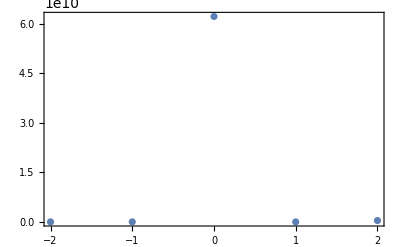
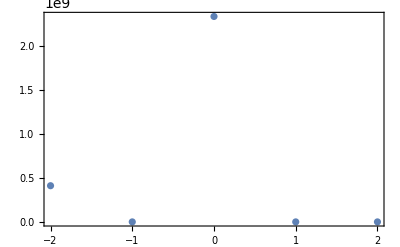

```mathematica
{ListPlot[tms1,Frame->True,Axes->False,PlotRange->Full],ListPlot[tmsm1,Frame->True,Axes->False,PlotRange->Full]}
```

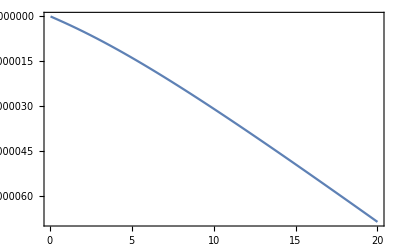

```mathematica
Plot[EqnSpecX[xx/mee,1/5,-1],{xx,1/20,20},Frame->True,PlotRange->Full]
```

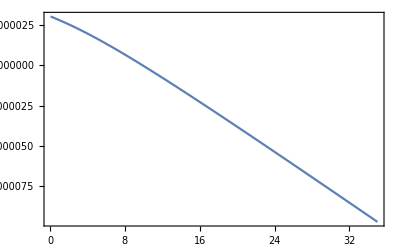

```mathematica
Plot[EqnSpecX[xx/mee,1/5,-2],{xx,1/20,35},Frame->True,PlotRange->Full]
```

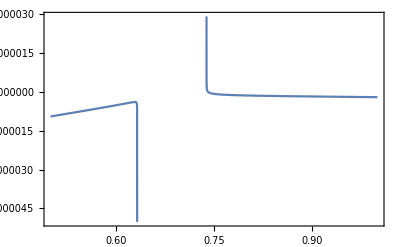

```mathematica
Plot[EqnSpecY[xx/mee,1/5,0],{xx,0.5,1},Frame->True,PlotRange->Full,PlotPoints->100]
```

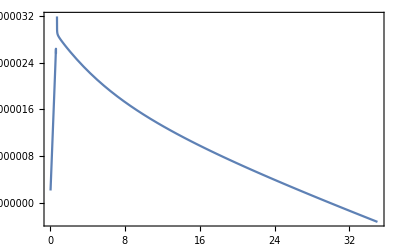

```mathematica
Plot[EqnSpecY[xx/mee,1/5,-1],{xx,1/20,35},Frame->True,PlotRange->Full]
```

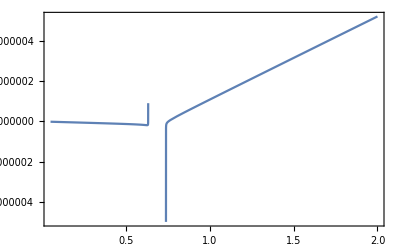

```mathematica
Plot[EqnSpecTY[xx/mee,1/5,-1],{xx,1/20,2},Frame->True,PlotRange->Full]
```

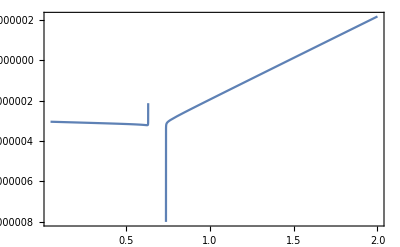

```mathematica
Plot[EqnSpecTY[xx/mee,1/5,-2],{xx,1/20,2},Frame->True,PlotRange->Full]
```

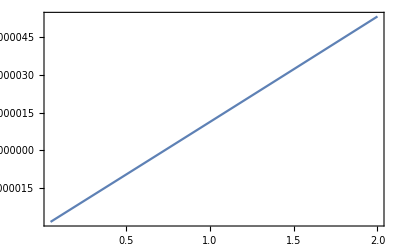

```mathematica
Plot[EqnSpecTX[xx/mee,1/5,-2],{xx,1/20,2},Frame->True,PlotRange->Full]
```

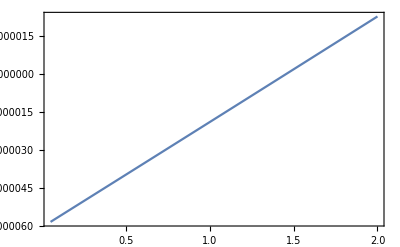

```mathematica
Plot[EqnSpecTX[xx/mee,1/5,-3],{xx,1/20,2},Frame->True,PlotRange->Full]
```

```mathematica
spectpl[1.5/mee,1/5,0] mee
spectpp[1.5/mee,1/5,0] mee
spectpl[1.5/mee,1/5,-1] mee
spectpp[1.5/mee,1/5,-1] mee
spect3pl[1.5/mee,1/5,-1] mee
spect3pp[1.5/mee,1/5,-1] mee
```

-3.3678857525609899308172939535832547389787129429361042273473069072958265269055638669317677

-25.82723557114880604857100363496592890087638165999410510450125200023270914044947575026135

3.3678857525609899308172939535832547389787129429361042273473069072958265269055638669317677

25.82723557114880604857100363496592890087638165999410510450125200023270914044947575026135

0.34816721712587189946825812554907012118106384195547023587877777244136158198254150450133933

0.37806515301769965441355125647507918119448355140262175100352464301008040472872494893776441

```mathematica
spectpl[1.5/mee,1/5,-2] mee
spectpp[1.5/mee,1/5,-1] mee
```

10.103657257682969792451881860749764216936138828808312682041920721887479580716691600795303

25.82723557114880604857100363496592890087638165999410510450125200023270914044947575026135

```mathematica
ϵpp[1.5/mee]-1
ϵpl[1.5/mee]-1
```

0.100000000000000088817841970012523233890533447265625

0.5

```mathematica
tk0s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/5,0]},{x,1,5,0.05}]
```

(1. | 16.9519
1.05 | 2046.45
1.1 | 7553.78
1.15 | 13946.7
1.2 | 18284.7
1.25 | 18849.3
1.3 | 15617.8
1.35 | 9911.71
1.4 | 4064.95
1.45 | 481.631
1.5 | 430.661
1.55 | 3597.84
1.6 | 8448.49
1.65 | 12772.1
1.7 | 14610.9
1.75 | 13217.2
1.8 | 9267.16
1.85 | 4471.91
1.9 | 919.298
1.95 | 93.6397
2. | 2121.16
2.05 | 5862.53
2.1 | 9514.05
2.15 | 11311.
2.2 | 10384.9
2.25 | 7255.92
2.3 | 3430.84
2.35 | 629.366
2.4 | 130.228
2.45 | 2101.33
2.5 | 5402.64
2.55 | 8295.93
2.6 | 9363.76
2.65 | 8065.17
2.7 | 5036.
2.75 | 1845.99
2.8 | 122.722
2.85 | 713.105
2.9 | 3325.23
2.95 | 6659.51
3. | 9033.47
3.05 | 9246.43
3.1 | 7200.12
3.15 | 3944.56
3.2 | 1113.6
3.25 | 43.3721
3.3 | 1084.79
3.35 | 3495.95
3.4 | 5851.92
3.45 | 6768.51
3.5 | 5718.23
3.55 | 3343.06
3.6 | 994.46
3.65 | 6.09236
3.7 | 1014.92
3.75 | 3521.97
3.8 | 6149.
3.85 | 7461.1
3.9 | 6760.65
3.95 | 4455.09
4. | 1814.44
4.05 | 248.626
4.1 | 523.149
4.15 | 2341.57
4.2 | 4522.12
4.25 | 5694.62
4.3 | 5143.73
4.35 | 3213.43
4.4 | 1058.49
4.45 | 10.1107
4.5 | 767.714
4.55 | 2906.68
4.6 | 5169.97
4.65 | 6247.68
4.7 | 5528.46
4.75 | 3455.85
4.8 | 1250.18
4.85 | 165.495
4.9 | 737.597
4.95 | 2468.61
5. | 4144.84)

```mathematica
tk0sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/5,0]},{x,1,5,0.05}]
```

(1. | 18870.5
1.05 | 9893.77
1.1 | 3113.92
1.15 | 127.796
1.2 | 996.183
1.25 | 4836.23
1.3 | 10131.6
1.35 | 14985.6
1.4 | 17903.
1.45 | 18205.
1.5 | 15995.9
1.55 | 11973.3
1.6 | 7349.8
1.65 | 3325.35
1.7 | 728.982
1.75 | 23.9739
1.8 | 1176.86
1.85 | 3643.29
1.9 | 6725.71
1.95 | 9704.56
2. | 11804.8
2.05 | 12498.6
2.1 | 11707.2
2.15 | 9633.02
2.2 | 6743.93
2.25 | 3779.17
2.3 | 1427.5
2.35 | 142.605
2.4 | 224.064
2.45 | 1644.33
2.5 | 3903.33
2.55 | 6315.7
2.6 | 8296.34
2.65 | 9364.57
2.7 | 9274.12
2.75 | 8165.34
2.8 | 6397.
2.85 | 4366.75
2.9 | 2503.11
2.95 | 1128.04
3. | 341.881
3.05 | 131.778
3.1 | 457.26
3.15 | 1280.71
3.2 | 2578.23
3.25 | 4203.44
3.3 | 5839.97
3.35 | 7148.03
3.4 | 7808.46
3.45 | 7562.85
3.5 | 6413.73
3.55 | 4664.85
3.6 | 2749.39
3.65 | 1128.06
3.7 | 194.124
3.75 | 61.4834
3.8 | 518.294
3.85 | 1250.32
3.9 | 2019.21
3.95 | 2708.31
4. | 3343.05
4.05 | 4001.56
4.1 | 4698.55
4.15 | 5324.88
4.2 | 5618.13
4.25 | 5317.86
4.3 | 4381.96
4.35 | 3000.43
4.4 | 1531.51
4.45 | 426.942
4.5 | 7.19718
4.55 | 253.934
4.6 | 875.847
4.65 | 1546.69
4.7 | 2053.43
4.75 | 2370.48
4.8 | 2659.14
4.85 | 3123.93
4.9 | 3831.99
4.95 | 4591.73
5. | 5026.13)

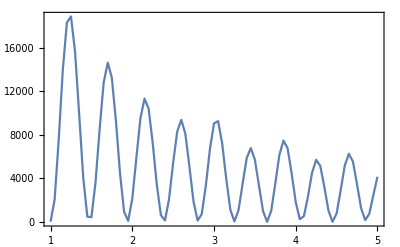
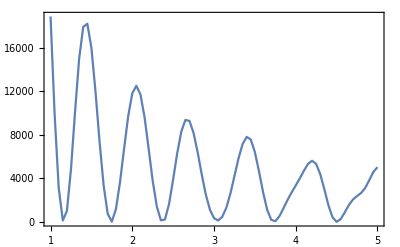

```mathematica
{ListLinePlot[tk0s1,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[tk0sm1,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
tk01s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/5,0]},{x,8,12,0.05}](*-2 гармоники не видно, т.к. соотв. коэффициент Фурье очень мал*)
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.24956×10^6}. NIntegrate obtained -4145.61+35675.7 ⅈ and 0.13511 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.18131×10^7}. NIntegrate obtained -33357.3-39399.3 ⅈ and 0.0919328 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.65958×10^7}. NIntegrate obtained -14506.5-66869.1 ⅈ and 0.097409 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.8721×10^7}. NIntegrate obtained -4422.77+6038.72 ⅈ and 0.143139 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.18131×10^7}. NIntegrate obtained 24796.8-76619. ⅈ and 0.102986 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {100394.}. NIntegrate obtained -5726.74+8646.29 ⅈ and 0.0448278 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.31925×10^7}. NIntegrate obtained 22110.7-2579.51 ⅈ and 0.151571 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained 27608.8+2290.15 ⅈ and 0.0478309 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14836×10^6}. NIntegrate obtained -15826.-50939.5 ⅈ and 0.0721004 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained 2059.42-26678.1 ⅈ and 0.076621 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained -8295.77-8748.82 ⅈ and 0.0813949 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.18131×10^7}. NIntegrate obtained -75122.9+15212.3 ⅈ and 0.19707 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.7664×10^7}. NIntegrate obtained -73223.8-4817.61 ⅈ and 0.286596 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.29752×10^6}. NIntegrate obtained 28362.9+12745.9 ⅈ and 0.405192 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.31925×10^7}. NIntegrate obtained -58013.7-9809.85 ⅈ and 0.564203 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.18131×10^7}. NIntegrate obtained -59188.8-25214.1 ⅈ and 0.207443 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.7664×10^7}. NIntegrate obtained -72238.5-61347.9 ⅈ and 0.302586 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.18131×10^7}. NIntegrate obtained 41583.2-1057.68 ⅈ and 0.426359 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.31925×10^7}. NIntegrate obtained -16762.7-17903.5 ⅈ and 0.592663 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.24467×10^7}. NIntegrate obtained -24809.8-41159.5 ⅈ and 0.218884 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.70194×10^7}. NIntegrate obtained -25625.5-106033. ⅈ and 0.317592 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.0745×10^7}. NIntegrate obtained 68127.7+18855.8 ⅈ and 0.447406 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.8721×10^7}. NIntegrate obtained 2082.13+11273.8 ⅈ and 0.623404 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained -16401.6-90950.5 ⅈ and 0.7839 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.48942×10^7}. NIntegrate obtained 70083.7-49579.7 ⅈ and 1.07973 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {100394.}. NIntegrate obtained 12204.6-6583.89 ⅈ and 1.40045 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.564×10^7}. NIntegrate obtained -54879.7-36294.3 ⅈ and 1.80029 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.65958×10^7}. NIntegrate obtained 32959.6-71237.5 ⅈ and 0.81901 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.29752×10^6}. NIntegrate obtained 95524.4+3291.17 ⅈ and 1.12615 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.65958×10^7}. NIntegrate obtained 37701.5+22152.4 ⅈ and 1.46543 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.564×10^7}. NIntegrate obtained -16911.9-41439.3 ⅈ and 1.87665 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained 48496.6-27733.3 ⅈ and 0.85686 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.18131×10^7}. NIntegrate obtained 71799.5+59305.3 ⅈ and 1.17394 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained 22939.9+63916.2 ⅈ and 1.53069 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.18131×10^7}. NIntegrate obtained 4376.63-19284.1 ⅈ and 1.95993 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

(8. | 2919.61
8.05 | 1655.96
8.1 | 368.583
8.15 | 42.0973
8.2 | 975.028
8.25 | 2565.35
8.3 | 3717.03
8.35 | 3631.98
8.4 | 2391.81
8.45 | 862.762
8.5 | 58.3972
8.55 | 412.616
8.6 | 1474.78
8.65 | 2310.02
8.7 | 2251.49
8.75 | 1384.45
8.8 | 451.102
8.85 | 246.588
8.9 | 963.395
8.95 | 2039.58
9. | 2599.32
9.05 | 2150.18
9.1 | 1019.39
9.15 | 114.151
9.2 | 202.443
9.25 | 1319.96
9.3 | 2716.95
9.35 | 3395.53
9.4 | 2874.41
9.45 | 1536.95
9.5 | 324.503
9.55 | 44.1971
9.6 | 754.441
9.65 | 1751.78
9.7 | 2184.04
9.75 | 1727.37
9.8 | 802.544
9.85 | 214.263
9.9 | 472.521
9.95 | 1367.02
10. | 2143.91
10.05 | 2120.84
10.1 | 1284.14
10.15 | 335.504
10.2 | 113.259
10.25 | 900.466
10.3 | 2178.11
10.35 | 2993.82
10.4 | 2715.26
10.45 | 1537.95
10.5 | 340.675
10.55 | 36.8106
10.6 | 855.217
10.65 | 2145.59
10.7 | 2913.74
10.75 | 2602.23
10.8 | 1470.52
10.85 | 371.513
10.9 | 67.6764
10.95 | 636.484
11. | 1472.04
11.05 | 1816.52
11.1 | 1392.46
11.15 | 618.866
11.2 | 212.978
11.25 | 546.354
11.3 | 1330.85
11.35 | 1858.23
11.4 | 1628.02
11.45 | 807.059
11.5 | 107.187
11.55 | 200.165
11.6 | 1137.99
11.65 | 2257.88
11.7 | 2708.04
11.75 | 2134.22
11.8 | 959.679
11.85 | 89.9857
11.9 | 187.799
11.95 | 1131.8
12. | 2145.64)

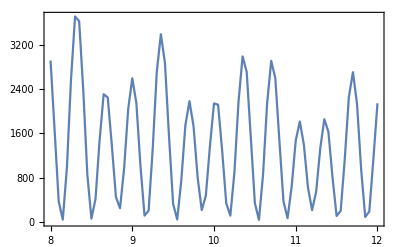

```mathematica
ListLinePlot[tk01s1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk01sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/5,0]},{x,6,14,0.05}](*-2 гармоники не видно, т.к. соотв. коэффициент Фурье очень мал*)
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.29752×10^6}. NIntegrate obtained -36934.6+107093. ⅈ and 0.276376 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.8721×10^7}. NIntegrate obtained -11280.4+169749. ⅈ and 0.172103 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {100394.}. NIntegrate obtained -145347.+25826.4 ⅈ and 0.291187 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.31925×10^7}. NIntegrate obtained -116811.+58262.5 ⅈ and 0.181805 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.18131×10^7}. NIntegrate obtained -111570.-131280. ⅈ and 0.306678 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.24467×10^7}. NIntegrate obtained 5548.-17961.9 ⅈ and 0.0619164 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.31925×10^7}. NIntegrate obtained -69154.8-54621.4 ⅈ and 0.19192 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.18131×10^7}. NIntegrate obtained 6276.7+35158.2 ⅈ and 0.0657332 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained -55900.3+28524.4 ⅈ and 0.0697079 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.77652×10^7}. NIntegrate obtained 263316.+42642.2 ⅈ and 0.456124 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.8721×10^7}. NIntegrate obtained 1276.18+4016.49 ⅈ and 0.734053 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained 231436.-51039.7 ⅈ and 1.15473 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.29752×10^6}. NIntegrate obtained 93505.6+223536. ⅈ and 0.479232 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained -24777.7-120550. ⅈ and 1.77806 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained -36201.6+33059.8 ⅈ and 0.769258 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.65958×10^7}. NIntegrate obtained -126347.+162347. ⅈ and 0.503268 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.45719×10^7}. NIntegrate obtained 154273.+171889. ⅈ and 1.20705 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.564×10^7}. NIntegrate obtained 86852.4-47002.7 ⅈ and 1.85418 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained -81317.9-19854.2 ⅈ and 0.805708 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.48942×10^7}. NIntegrate obtained -80366.9+202297. ⅈ and 1.26089 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.564×10^7}. NIntegrate obtained 62198.8+63286.5 ⅈ and 1.93245 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.48942×10^7}. NIntegrate obtained 103675.-69755.9 ⅈ and 2.68469 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.18131×10^7}. NIntegrate obtained -57385.1-195868. ⅈ and 3.9808 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained 110123.+68092.7 ⅈ and 2.79339 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.28702×10^7}. NIntegrate obtained -82309.9-1006.59 ⅈ and 5.80737 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.45719×10^7}. NIntegrate obtained -49414.7-161907. ⅈ and 8.35035 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.53177×10^7}. NIntegrate obtained 161886.-135030. ⅈ and 4.13495 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained -30360.5-48122.8 ⅈ and 6.02589 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.65958×10^7}. NIntegrate obtained -29010.4+135641. ⅈ and 2.90604 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained 200974.+86189.7 ⅈ and 4.29611 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.94668×10^7}. NIntegrate obtained 137451.-141634. ⅈ and 8.65724 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained 8021.63-19044.5 ⅈ and 6.2543 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.48942×10^7}. NIntegrate obtained 207389.+51212.7 ⅈ and 8.97307 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

(6. | 1312.75
6.05 | 832.781
6.1 | 771.418
6.15 | 784.673
6.2 | 605.099
6.25 | 262.273
6.3 | 34.4002
6.35 | 220.871
6.4 | 931.952
6.45 | 1979.93
6.5 | 2932.59
6.55 | 3361.64
6.6 | 3145.95
6.65 | 2576.45
6.7 | 2133.41
6.75 | 2141.65
6.8 | 2576.37
6.85 | 3092.73
6.9 | 3232.64
6.95 | 2733.93
7. | 1748.38
7.05 | 738.047
7.1 | 139.333
7.15 | 77.5198
7.2 | 336.351
7.25 | 570.664
7.3 | 565.846
7.35 | 395.05
7.4 | 390.485
7.45 | 887.053
7.5 | 1894.88
7.55 | 3021.23
7.6 | 3718.75
7.65 | 3654.78
7.7 | 2941.97
7.75 | 2052.98
7.8 | 1508.75
7.85 | 1558.96
7.9 | 2010.43
7.95 | 2354.99
8. | 2179.69
8.05 | 1486.32
8.1 | 645.148
8.15 | 98.6282
8.2 | 52.8608
8.25 | 360.815
8.3 | 664.045
8.35 | 676.23
8.4 | 433.116
8.45 | 306.736
8.5 | 684.51
8.55 | 1597.19
8.6 | 2653.07
8.65 | 3294.65
8.7 | 3189.52
8.75 | 2474.73
8.8 | 1658.47
8.85 | 1281.99
8.9 | 1557.42
8.95 | 2187.08
9. | 2586.6
9.05 | 2364.09
9.1 | 1589.64
9.15 | 696.571
9.2 | 149.787
9.25 | 115.974
9.3 | 385.026
9.35 | 576.553
9.4 | 455.921
9.45 | 154.943
9.5 | 74.2491
9.55 | 497.144
9.6 | 1304.73
9.65 | 2037.98
9.7 | 2248.13
9.75 | 1871.32
9.8 | 1292.66
9.85 | 1060.85
9.9 | 1499.66
9.95 | 2426.95
10. | 3229.22
10.05 | 3330.9
10.1 | 2624.74
10.15 | 1530.46
10.2 | 686.408
10.25 | 477.147
10.3 | 779.041
10.35 | 1134.81
10.4 | 1128.77
10.45 | 697.084
10.5 | 179.1
10.55 | 6.39733
10.6 | 309.388
10.65 | 804.283
10.7 | 1041.78
10.75 | 832.436
10.8 | 445.52
10.85 | 365.762
10.9 | 886.987
10.95 | 1848.6
11. | 2697.07
11.05 | 2893.87
11.1 | 2338.85
11.15 | 1465.03
11.2 | 947.153
11.25 | 1174.36
11.3 | 1914.61
11.35 | 2539.92
11.4 | 2530.
11.45 | 1834.09
11.5 | 891.634
11.55 | 276.016
11.6 | 249.736
11.65 | 604.839
11.7 | 866.019
11.75 | 713.643
11.8 | 283.301
11.85 | 5.22064
11.9 | 179.658
11.95 | 700.566
12. | 1139.9
12.05 | 1139.88
12.1 | 749.569
12.15 | 394.026
12.2 | 546.762
12.25 | 1315.47
12.3 | 2276.88
12.35 | 2791.44
12.4 | 2513.18
12.45 | 1676.95
12.5 | 952.057
12.55 | 902.809
12.6 | 1518.3
12.65 | 2266.63
12.7 | 2521.45
12.75 | 2031.01
12.8 | 1113.2
12.85 | 377.
12.9 | 226.637
12.95 | 570.703
13. | 928.145
13.05 | 880.22
13.1 | 458.74
13.15 | 62.0279
13.2 | 57.8114
13.25 | 448.211
13.3 | 867.475
13.35 | 932.333
13.4 | 604.562
13.45 | 245.576
13.5 | 334.945
13.55 | 1019.71
13.6 | 1918.25
13.65 | 2414.92
13.7 | 2163.24
13.75 | 1401.86
13.8 | 805.913
13.85 | 911.208
13.9 | 1663.51
13.95 | 2487.
14. | 2726.63)

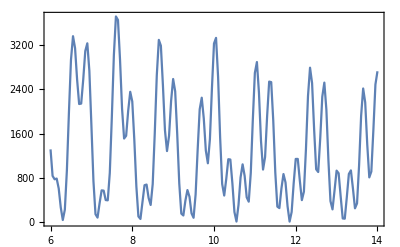

```mathematica
ListLinePlot[tk01sm1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk02s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/5,0]},{x,26,34,0.05}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.11685×10^7}. NIntegrate obtained -416117.-52056.2 ⅈ and 4173.5 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.65958×10^7}. NIntegrate obtained 97043.9-29399.5 ⅈ and 3192.06 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.25479×10^7}. NIntegrate obtained -140528.-435433. ⅈ and 4287.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.6697×10^7}. NIntegrate obtained 50373.6+65370.4 ⅈ and 3248.03 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.28702×10^7}. NIntegrate obtained 350502.-341851. ⅈ and 4355.88 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.8721×10^7}. NIntegrate obtained -25618.8+59683.6 ⅈ and 3307.62 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.65958×10^7}. NIntegrate obtained -277787.+260972. ⅈ and 5419.75 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.6697×10^7}. NIntegrate obtained -320123.-109580. ⅈ and 5499.78 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.53177×10^7}. NIntegrate obtained 46543.3-716314. ⅈ and 6872.79 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.48942×10^7}. NIntegrate obtained 746778.-312386. ⅈ and 6984.06 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.11685×10^7}. NIntegrate obtained -41069.9-279372. ⅈ and 5580.66 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.45719×10^7}. NIntegrate obtained 672854.+586084. ⅈ and 7086.25 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.0745×10^7}. NIntegrate obtained -1.40737×10^6-1.43795×10^6 ⅈ and 8665.13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.31925×10^7}. NIntegrate obtained -2.3257×10^6-37406.2 ⅈ and 10603.1 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.24467×10^7}. NIntegrate obtained 717557.-1.93022×10^6 ⅈ and 8791.65 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.45719×10^7}. NIntegrate obtained -955144.-2.10762×10^6 ⅈ and 10967.8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14836×10^6}. NIntegrate obtained 2.10388×10^6-170406. ⅈ and 8920.45 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.8721×10^7}. NIntegrate obtained 1.47752×10^6-1.75238×10^6 ⅈ and 11124.9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.18131×10^7}. NIntegrate obtained -1.01094×10^6+977840. ⅈ and 12884.4 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained -8288.04+73202.9 ⅈ and 16438.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.65958×10^7}. NIntegrate obtained -1.23151×10^6-456455. ⅈ and 13570.4 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.0745×10^7}. NIntegrate obtained -14054.-13628.6 ⅈ and 16640.1 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained -105266.-1.21324×10^6 ⅈ and 13526.5 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14836×10^6}. NIntegrate obtained 51163.7+10639.4 ⅈ and 16843.9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.8721×10^7}. NIntegrate obtained -350096.-356270. ⅈ and 19926.6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.65958×10^7}. NIntegrate obtained 180141.-462164. ⅈ and 20143. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.11685×10^7}. NIntegrate obtained -222430.-35906.7 ⅈ and 24124.8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.93656×10^7}. NIntegrate obtained 498399.-22619.5 ⅈ and 20324.7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.90433×10^7}. NIntegrate obtained -56742.3-196110. ⅈ and 24368.4 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.69182×10^7}. NIntegrate obtained 126620.-121096. ⅈ and 24671. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

(26. | 133.953
26.05 | 5.32666
26.1 | 235.18
26.15 | 649.163
26.2 | 1009.59
26.25 | 1102.6
26.3 | 885.329
26.35 | 469.563
26.4 | 99.4682
26.45 | 30.4952
26.5 | 381.665
26.55 | 1025.12
26.6 | 1605.33
26.65 | 1733.08
26.7 | 1299.59
26.75 | 608.309
26.8 | 223.968
26.85 | 563.506
26.9 | 1557.15
26.95 | 2540.3
27. | 2833.08
27.05 | 2224.19
27.1 | 1190.77
27.15 | 597.342
27.2 | 983.205
27.25 | 2104.86
27.3 | 3125.64
27.35 | 3264.55
27.4 | 2400.39
27.45 | 1195.32
27.5 | 516.237
27.55 | 757.688
27.6 | 1575.
27.65 | 2209.93
27.7 | 2125.23
27.75 | 1408.45
27.8 | 571.508
27.85 | 82.1209
27.9 | 47.4852
27.95 | 268.534
28. | 550.633
28.05 | 872.761
28.1 | 1258.41
28.15 | 1543.78
28.2 | 1473.05
28.25 | 1041.2
28.3 | 750.725
28.35 | 1388.18
28.4 | 3313.13
28.45 | 5907.19
28.5 | 7767.07
28.55 | 8036.14
28.6 | 7092.94
28.65 | 6759.24
28.7 | 8860.95
28.75 | 13491.4
28.8 | 18704.5
28.85 | 21902.2
28.9 | 21880.4
28.95 | 20314.1
29. | 20546.3
29.05 | 24732.8
29.1 | 31996.6
29.15 | 38757.9
29.2 | 41358.2
29.25 | 39561.4
29.3 | 36827.
29.35 | 37456.5
29.4 | 43324.5
29.45 | 51896.2
29.5 | 57935.9
29.55 | 58281.
29.6 | 54336.
29.65 | 50762.3
29.7 | 52182.1
29.75 | 58976.6
29.8 | 66577.4
29.85 | 69619.5
29.9 | 66170.
29.95 | 59059.6
30. | 54175.
30.05 | 55136.5
30.1 | 60637.7
30.15 | 65026.5
30.2 | 63860.1
30.25 | 56911.7
30.3 | 48689.7
30.35 | 44601.9
30.4 | 46055.3
30.45 | 49953.5
30.5 | 51142.2
30.55 | 46876.1
30.6 | 38721.5
30.65 | 31537.7
30.7 | 28565.7
30.75 | 29581.9
30.8 | 31159.9
30.85 | 29686.2
30.9 | 24231.7
30.95 | 17626.8
31. | 12990.4
31.05 | 11903.2
31.1 | 12940.8
31.15 | 13176.2
31.2 | 10994.4
31.25 | 7206.39
31.3 | 3862.67
31.35 | 2487.67
31.4 | 2797.57
31.45 | 3290.51
31.5 | 2821.05
31.55 | 1477.86
31.6 | 292.701
31.65 | 55.893
31.7 | 556.063
31.75 | 933.16
31.8 | 678.789
31.85 | 189.158
31.9 | 303.041
31.95 | 1361.31
32. | 2702.4
32.05 | 3273.51
32.1 | 2705.56
32.15 | 1753.93
32.2 | 1628.07
32.25 | 2913.48
32.3 | 4823.25
32.35 | 5934.45
32.4 | 5402.44
32.45 | 3802.23
32.5 | 2622.04
32.55 | 2943.85
32.6 | 4529.89
32.65 | 5922.47
32.7 | 5873.78
32.75 | 4343.84
32.8 | 2550.52
32.85 | 1856.33
32.9 | 2593.08
32.95 | 3788.05
33. | 4161.16
33.05 | 3246.5
33.1 | 1713.84
33.15 | 696.731
33.2 | 749.289
33.25 | 1435.57
33.3 | 1842.19
33.35 | 1473.
33.4 | 633.363
33.45 | 57.6273
33.5 | 146.666
33.55 | 606.312
33.6 | 822.506
33.65 | 535.653
33.7 | 94.507
33.75 | 78.6934
33.8 | 648.82
33.85 | 1335.07
33.9 | 1503.58
33.95 | 1015.26
34. | 416.821)

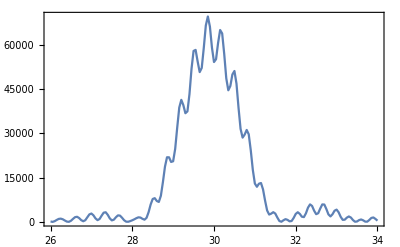

```mathematica
ListLinePlot[tk02s1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk02sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/5,0]},{x,26,34,0.05}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained 648953.+46185.4 ⅈ and 4507.92 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained -181827.+32983.5 ⅈ and 3426.55 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained 248918.+626370. ⅈ and 4579.56 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.70194×10^7}. NIntegrate obtained -79861.-103919. ⅈ and 3482.59 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained -475351.+503956. ⅈ and 4652.8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained 36255.6-64389.9 ⅈ and 3539.49 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained 389838.-338616. ⅈ and 5776.18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained 418511.+194482. ⅈ and 5865.01 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.70194×10^7}. NIntegrate obtained -18225.2+988278. ⅈ and 7329.3 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained -2374.36+406822. ⅈ and 5955.21 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained -1.01289×10^6+445505. ⅈ and 7437.37 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.31925×10^7}. NIntegrate obtained -926328.-815148. ⅈ and 7546.46 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained 1.90407×10^6+2.01071×10^6 ⅈ and 9210.95 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained -1.03015×10^6+2.66305×10^6 ⅈ and 9340.84 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained -2.92037×10^6+222886. ⅈ and 9471.45 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained 3.16265×10^6+52957.4 ⅈ and 11473.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained 1.28745×10^6+2.83635×10^6 ⅈ and 11627. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained -1.98241×10^6+2.33235×10^6 ⅈ and 11781.8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.45719×10^7}. NIntegrate obtained 1.31806×10^6-1.27211×10^6 ⅈ and 14163.5 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained 1.60919×10^6+615859. ⅈ and 14344.8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.48942×10^7}. NIntegrate obtained 122731.+1.61217×10^6 ⅈ and 14529.4 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained -1692.34-118595. ⅈ and 17348.9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.48942×10^7}. NIntegrate obtained 25649.5-26104.4 ⅈ and 17567.3 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.29752×10^6}. NIntegrate obtained -27696.7-49504.7 ⅈ and 17776.2 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.564×10^7}. NIntegrate obtained 429760.+483890. ⅈ and 21043.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained 286863.+404.66 ⅈ and 25394.5 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.564×10^7}. NIntegrate obtained -250583.+606968. ⅈ and 21312.5 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.8721×10^7}. NIntegrate obtained 102293.+215314. ⅈ and 25695.7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained -126972.+147249. ⅈ and 25988.8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.564×10^7}. NIntegrate obtained -652924.+40545.6 ⅈ and 21576.9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

(26. | 1101.26
26.05 | 339.597
26.1 | 11.6587
26.15 | 228.135
26.2 | 556.509
26.25 | 532.235
26.3 | 217.974
26.35 | 167.676
26.4 | 822.442
26.45 | 1982.09
26.5 | 2893.99
26.55 | 2972.68
26.6 | 2447.48
26.65 | 2247.1
26.7 | 3194.43
26.75 | 5217.3
26.8 | 7043.69
26.85 | 7665.08
26.9 | 6862.25
26.95 | 5687.91
27. | 5596.79
27.05 | 7110.93
27.1 | 9276.04
27.15 | 10491.1
27.2 | 9847.71
27.25 | 7904.57
27.3 | 6255.03
27.35 | 6104.55
27.4 | 7249.02
27.45 | 8326.87
27.5 | 8007.02
27.55 | 6147.72
27.6 | 3875.87
27.65 | 2494.2
27.7 | 2378.78
27.75 | 2780.01
27.8 | 2650.65
27.85 | 1682.19
27.9 | 529.781
27.95 | 15.1924
28. | 288.653
28.05 | 749.291
28.1 | 821.142
28.15 | 732.475
28.2 | 1405.5
28.25 | 3511.04
28.3 | 6591.46
28.35 | 9290.37
28.4 | 10632.8
28.45 | 11131.3
28.5 | 12671.2
28.55 | 16914.9
28.6 | 23550.6
28.65 | 30298.1
28.7 | 34715.5
28.75 | 36327.6
28.8 | 37485.6
28.85 | 41552.6
28.9 | 49824.1
28.95 | 60191.6
29. | 68521.2
29.05 | 71945.3
29.1 | 71730.9
29.15 | 72346.6
29.2 | 77583.9
29.25 | 87340.3
29.3 | 97325.1
29.35 | 102540.
29.4 | 101855.
29.45 | 98797.8
29.5 | 98515.1
29.55 | 103790.
29.6 | 112515.
29.65 | 119289.
29.7 | 120037.
29.75 | 115021.
29.8 | 108547.
29.85 | 105894.
29.9 | 108776.
29.95 | 113713.
30. | 115044.
30.05 | 109578.
30.1 | 99379.2
30.15 | 90269.4
30.2 | 86668.8
30.25 | 87955.2
30.3 | 89398.8
30.35 | 86284.8
30.4 | 77810.7
30.45 | 67524.7
30.5 | 59948.6
30.55 | 56959.1
30.6 | 56734.1
30.65 | 55324.4
30.7 | 50608.9
30.75 | 42362.5
30.8 | 33957.1
30.85 | 28340.1
30.9 | 26249.8
30.95 | 25775.8
31. | 24145.5
31.05 | 20072.2
31.1 | 14636.6
31.15 | 10061.9
31.2 | 7735.29
31.25 | 7263.29
31.3 | 7135.11
31.35 | 6128.82
31.4 | 4192.33
31.45 | 2155.63
31.5 | 827.566
31.55 | 369.979
31.6 | 379.666
31.65 | 418.684
31.7 | 399.142
31.75 | 493.554
31.8 | 759.561
31.85 | 981.225
31.9 | 904.276
31.95 | 636.206
32. | 609.985
32.05 | 1220.86
32.1 | 2351.66
32.15 | 3335.24
32.2 | 3560.27
32.25 | 2959.42
32.3 | 2162.77
32.35 | 1985.01
32.4 | 2728.32
32.45 | 3891.12
32.5 | 4590.92
32.55 | 4252.5
32.6 | 3112.68
32.65 | 2055.43
32.7 | 1837.09
32.75 | 2475.48
32.8 | 3281.06
32.85 | 3456.15
32.9 | 2764.68
32.95 | 1673.56
33. | 896.465
33.05 | 807.547
33.1 | 1214.63
33.15 | 1594.03
33.2 | 1549.58
33.25 | 1079.57
33.3 | 492.604
33.35 | 115.579
33.4 | 58.4514
33.45 | 204.325
33.5 | 375.478
33.55 | 473.359
33.6 | 486.085
33.65 | 426.417
33.7 | 283.069
33.75 | 109.322
33.8 | 15.5554
33.85 | 136.801
33.9 | 479.817
33.95 | 867.087
34. | 1037.22)

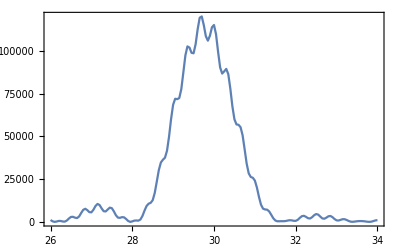

```mathematica
ListLinePlot[tk02sm1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
llt2s1=AmplTwistTab[1,29.8/mee,29.8/mee/5];
llt2sm1=AmplTwistTab[-1,29.8/mee,29.8/mee/5];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.54002×10^7}. NIntegrate obtained -1.93208×10^6-1.42899×10^6 ⅈ and 10349.2 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.24467×10^7}. NIntegrate obtained -1.90331×10^6-1.45677×10^6 ⅈ and 10116.8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.7203×10^7}. NIntegrate obtained -1.93266×10^6-1.42977×10^6 ⅈ and 10376.2 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.77652×10^7}. NIntegrate obtained -1.90562×10^6-1.45356×10^6 ⅈ and 10119.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.30539×10^7}. NIntegrate obtained -1.93304×10^6-1.43089×10^6 ⅈ and 10403.4 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.24956×10^6}. NIntegrate obtained -1.90794×10^6-1.45042×10^6 ⅈ and 10122.9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.42045×10^7}. NIntegrate obtained -1.91614×10^6-1.47065×10^6 ⅈ and 10575.5 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.64236×10^6}. NIntegrate obtained -1.88429×10^6-1.49616×10^6 ⅈ and 10356.2 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.60074×10^7}. NIntegrate obtained -1.91369×10^6-1.47398×10^6 ⅈ and 10570.8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.48117×10^7}. NIntegrate obtained -1.88385×10^6-1.49527×10^6 ⅈ and 10329. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.18582×10^7}. NIntegrate obtained -1.91117×10^6-1.47717×10^6 ⅈ and 10568. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.48117×10^7}. NIntegrate obtained -1.88367×10^6-1.49409×10^6 ⅈ and 10301.7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.24467×10^7}. NIntegrate obtained -1.90331×10^6-1.45677×10^6 ⅈ and 10116.8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.54002×10^7}. NIntegrate obtained -1.93208×10^6-1.42899×10^6 ⅈ and 10349.2 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.77652×10^7}. NIntegrate obtained -1.90562×10^6-1.45355×10^6 ⅈ and 10119.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.7203×10^7}. NIntegrate obtained -1.93267×10^6-1.42977×10^6 ⅈ and 10376.2 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.24956×10^6}. NIntegrate obtained -1.90794×10^6-1.45041×10^6 ⅈ and 10122.9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.30539×10^7}. NIntegrate obtained -1.93304×10^6-1.4309×10^6 ⅈ and 10403.4 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.42045×10^7}. NIntegrate obtained -1.91615×10^6-1.47066×10^6 ⅈ and 10575.5 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.60074×10^7}. NIntegrate obtained -1.9137×10^6-1.47398×10^6 ⅈ and 10570.8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.64236×10^6}. NIntegrate obtained -1.88429×10^6-1.49617×10^6 ⅈ and 10356.2 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.18582×10^7}. NIntegrate obtained -1.91118×10^6-1.47718×10^6 ⅈ and 10568. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.48117×10^7}. NIntegrate obtained -1.88385×10^6-1.49528×10^6 ⅈ and 10329. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.48117×10^7}. NIntegrate obtained -1.88367×10^6-1.49409×10^6 ⅈ and 10301.7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.33762×10^7}. NIntegrate obtained -1.97853×10^6+2.5427×10^6 ⅈ and 10925.4 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained 2.56317×10^6+1.97293×10^6 ⅈ and 10716.6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.33762×10^7}. NIntegrate obtained -2.21714×10^6+2.33556×10^6 ⅈ and 10950. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained 2.35632×10^6+2.21593×10^6 ⅈ and 10722.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.03963×10^7}. NIntegrate obtained -2.43409×10^6+2.10625×10^6 ⅈ and 10970.5 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.1592×10^7}. NIntegrate obtained 2.12646×10^6+2.43726×10^6 ⅈ and 10726.3 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.21805×10^7}. NIntegrate obtained -2.54118×10^6-1.95303×10^6 ⅈ and 11125. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.09848×10^7}. NIntegrate obtained 1.94849×10^6-2.563×10^6 ⅈ and 10926.1 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.80313×10^7}. NIntegrate obtained -2.33875×10^6-2.19134×10^6 ⅈ and 11128.4 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.68357×10^7}. NIntegrate obtained 2.19151×10^6-2.36054×10^6 ⅈ and 10910.7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.98342×10^7}. NIntegrate obtained -2.11416×10^6-2.40892×10^6 ⅈ and 11126.1 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.86385×10^7}. NIntegrate obtained 2.4137×10^6-2.13497×10^6 ⅈ and 10890.3 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained 2.56317×10^6+1.97293×10^6 ⅈ and 10716.6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained 2.35632×10^6+2.21593×10^6 ⅈ and 10722.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.33762×10^7}. NIntegrate obtained -1.97854×10^6+2.54271×10^6 ⅈ and 10925.4 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.1592×10^7}. NIntegrate obtained 2.12646×10^6+2.43727×10^6 ⅈ and 10726.3 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.33762×10^7}. NIntegrate obtained -2.21715×10^6+2.33556×10^6 ⅈ and 10950. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.03963×10^7}. NIntegrate obtained -2.43409×10^6+2.10625×10^6 ⅈ and 10970.5 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.21805×10^7}. NIntegrate obtained -2.54119×10^6-1.95304×10^6 ⅈ and 11125. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.80313×10^7}. NIntegrate obtained -2.33876×10^6-2.19134×10^6 ⅈ and 11128.4 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.09848×10^7}. NIntegrate obtained 1.94849×10^6-2.56301×10^6 ⅈ and 10926.1 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.98342×10^7}. NIntegrate obtained -2.11416×10^6-2.40893×10^6 ⅈ and 11126.1 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.68357×10^7}. NIntegrate obtained 2.19152×10^6-2.36054×10^6 ⅈ and 10910.7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.86385×10^7}. NIntegrate obtained 2.4137×10^6-2.13497×10^6 ⅈ and 10890.3 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
tm2s1=Table[{m,dProbabTwist[m,llt2s1[[3]]]},{m,-mMax,mMax}];
tm2sm1=Table[{m,dProbabTwist[m,llt2sm1[[3]]]},{m,-mMax,mMax}];
```

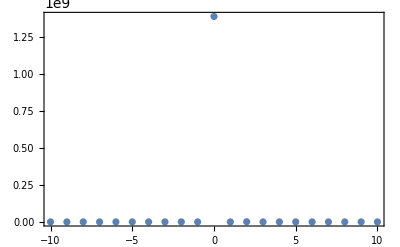
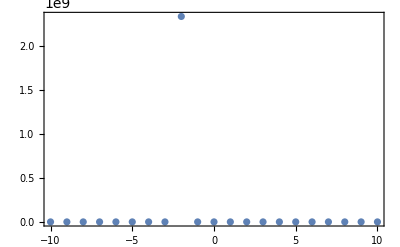

```mathematica
{ListPlot[tm2s1,Frame->True,Axes->False,PlotRange->Full],ListPlot[tm2sm1,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
tk0=ParallelTable[{x,dProbabPlane[-1,x/mee,1/γ,0]},{x,0.01,1,0.01/4}](*ТВ не работает в окрестности щели*)
tk0m1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/γ,0]},{x,0.01,1,0.01/4}]
```

(0.01 | 5.47105×10^6
0.0125 | 6.60793×10^6
0.015 | 7.72229×10^6
0.0175 | 8.87571×10^6
0.02 | 1.01152×10^7
0.0225 | 1.14574×10^7
0.025 | 1.28813×10^7
0.0275 | 1.43338×10^7
0.03 | 1.57484×10^7
0.0325 | 1.70693×10^7
0.035 | 1.82716×10^7
0.0375 | 1.93683×10^7
0.04 | 2.04041×10^7
0.0425 | 2.1439×10^7
0.045 | 2.25287×10^7
0.0475 | 2.37065×10^7
0.05 | 2.49711×10^7
0.0525 | 2.6286×10^7
0.055 | 2.75904×10^7
0.0575 | 2.88213×10^7
0.06 | 2.99364×10^7
0.0625 | 3.09289×10^7
0.065 | 3.18281×10^7
0.0675 | 3.26878×10^7
0.07 | 3.35673×10^7
0.0725 | 3.45122×10^7
0.075 | 3.55396×10^7
0.0775 | 3.66315×10^7
0.08 | 3.77392×10^7
0.0825 | 3.87999×10^7
0.085 | 3.97591×10^7
0.0875 | 4.05911×10^7
0.09 | 4.13072×10^7
0.0925 | 4.19496×10^7
0.095 | 4.25763×10^7
0.0975 | 4.32408×10^7
0.1 | 4.39754×10^7
0.1025 | 4.47803×10^7
0.105 | 4.56227×10^7
0.1075 | 4.64467×10^7
0.11 | 4.71926×10^7
0.1125 | 4.78191×10^7
0.115 | 4.83183×10^7
0.1175 | 4.87174×10^7
0.12 | 4.90678×10^7
0.1225 | 4.94261×10^7
0.125 | 4.98362×10^7
0.1275 | 5.0315×10^7
0.13 | 5.0847×10^7
0.1325 | 5.13881×10^7
0.135 | 5.18801×10^7
0.1375 | 5.22715×10^7
0.14 | 5.25366×10^7
0.1425 | 5.26848×10^7
0.145 | 5.27561×10^7
0.1475 | 5.28055×10^7
0.15 | 5.28845×10^7
0.1525 | 5.30242×10^7
0.155 | 5.3226×10^7
0.1575 | 5.3461×10^7
0.16 | 5.36783×10^7
0.1625 | 5.38227×10^7
0.165 | 5.38542×10^7
0.1675 | 5.37635×10^7
0.17 | 5.35751×10^7
0.1725 | 5.3337×10^7
0.175 | 5.31035×10^7
0.1775 | 5.29169×10^7
0.18 | 5.27945×10^7
0.1825 | 5.27237×10^7
0.185 | 5.26658×10^7
0.1875 | 5.25682×10^7
0.19 | 5.23824×10^7
0.1925 | 5.20823×10^7
0.195 | 5.16739×10^7
0.1975 | 5.11929×10^7
0.2 | 5.06908×10^7
0.2025 | 5.02163×10^7
0.205 | 4.98006×10^7
0.2075 | 4.94475×10^7
0.21 | 4.91333×10^7
0.2125 | 4.88139×10^7
0.215 | 4.84393×10^7
0.2175 | 4.79711×10^7
0.22 | 4.73974×10^7
0.2225 | 4.67368×10^7
0.225 | 4.60317×10^7
0.2275 | 4.53318×10^7
0.23 | 4.46776×10^7
0.2325 | 4.40878×10^7
0.235 | 4.35549×10^7
0.2375 | 4.30476×10^7
0.24 | 4.25211×10^7
0.2425 | 4.1932×10^7
0.245 | 4.12537×10^7
0.2475 | 4.0487×10^7
0.25 | 3.96594×10^7
0.2525 | 3.8815×10^7
0.255 | 3.79977×10^7
0.2575 | 3.72375×10^7
0.26 | 3.65415×10^7
0.2625 | 3.58935×10^7
0.265 | 3.52592×10^7
0.2675 | 3.45972×10^7
0.27 | 3.38734×10^7
0.2725 | 3.30733×10^7
0.275 | 3.22077×10^7
0.2775 | 3.13086×10^7
0.28 | 3.0417×10^7
0.2825 | 2.95681×10^7
0.285 | 2.87805×10^7
0.2875 | 2.8052×10^7
0.29 | 2.7361×10^7
0.2925 | 2.66743×10^7
0.295 | 2.59576×10^7
0.2975 | 2.51876×10^7
0.3 | 2.43603×10^7
0.3025 | 2.34933×10^7
0.305 | 2.26183×10^7
0.3075 | 2.17695×10^7
0.31 | 2.09715×10^7
0.3125 | 2.02325×10^7
0.315 | 1.95434×10^7
0.3175 | 1.88815×10^7
0.32 | 1.82182×10^7
0.3225 | 1.75286×10^7
0.325 | 1.67999×10^7
0.3275 | 1.60367×10^7
0.33 | 1.52589×10^7
0.3325 | 1.44941×10^7
0.335 | 1.37668×10^7
0.3375 | 1.30909×10^7
0.34 | 1.24663×10^7
0.3425 | 1.18802×10^7
0.345 | 1.13124×10^7
0.3475 | 1.0742×10^7
0.35 | 1.01539×10^7
0.3525 | 9.54491×10^6
0.355 | 8.92433×10^6
0.3575 | 8.3106×10^6
0.36 | 7.72364×10^6
0.3625 | 7.17763×10^6
0.365 | 6.6769×10^6
0.3675 | 6.21592×10^6
0.37 | 5.78228×10^6
0.3725 | 5.3612×10^6
0.375 | 4.94049×10^6
0.3775 | 4.51459×10^6
0.38 | 4.08658×10^6
0.3825 | 3.66676×10^6
0.385 | 3.26827×10^6
0.3875 | 2.90174×10^6
0.39 | 2.57171×10^6
0.3925 | 2.27602×10^6
0.395 | 2.0077×10^6
0.3975 | 1.75802×10^6
0.4 | 1.51959×10^6
0.4025 | 1.28872×10^6
0.405 | 1.06658×10^6
0.4075 | 858385.
0.41 | 670910.
0.4125 | 509393.
0.415 | 375509.
0.4175 | 267331.
0.42 | 180890.
0.4225 | 112249.
0.425 | 59150.1
0.4275 | 21741.4
0.43 | 2199.14
0.4325 | 3323.26
0.435 | 26681.7
0.4375 | 71355.9
0.44 | 134186.
0.4425 | 211432.
0.445 | 300831.
0.4475 | 402944.
0.45 | 521293.
0.4525 | 661224.
0.455 | 827663.
0.4575 | 1.02225×10^6
0.46 | 1.24112×10^6
0.4625 | 1.47518×10^6
0.465 | 1.71358×10^6
0.4675 | 1.94881×10^6
0.47 | 2.1804×10^6
0.4725 | 2.41549×10^6
0.475 | 2.6665×10^6
0.4775 | 2.94721×10^6
0.48 | 3.26781×10^6
0.4825 | 3.62954×10^6
0.485 | 4.02088×10^6
0.4875 | 4.41888×10^6
0.49 | 4.79782×10^6
0.4925 | 5.14168×10^6
0.495 | 5.45243×10^6
0.4975 | 5.7493×10^6
0.5 | 6.06137×10^6
0.5025 | 6.41824×10^6
0.505 | 6.84082×10^6
0.5075 | 7.33195×10^6
0.51 | 7.86875×10^6
0.5125 | 8.40329×10^6
0.515 | 8.87932×10^6
0.5175 | 9.26082×10^6
0.52 | 9.55277×10^6
0.5225 | 9.79841×10^6
0.525 | 1.00594×10^7
0.5275 | 1.03949×10^7
0.53 | 1.08453×10^7
0.5325 | 1.14176×10^7
0.535 | 1.20708×10^7
0.5375 | 1.27108×10^7
0.54 | 1.32193×10^7
0.5425 | 1.35194×10^7
0.545 | 1.36274×10^7
0.5475 | 1.36423×10^7
0.55 | 1.36915×10^7
0.5525 | 1.38831×10^7
0.555 | 1.42828×10^7
0.5575 | 1.48966×10^7
0.56 | 1.56399×10^7
0.5625 | 1.63168×10^7
0.565 | 1.66796×10^7
0.5675 | 1.65975×10^7
0.57 | 1.61768×10^7
0.5725 | 1.56762×10^7
0.575 | 1.53394×10^7
0.5775 | 1.53181×10^7
0.58 | 1.56721×10^7
0.5825 | 1.63488×10^7
0.585 | 1.70933×10^7
0.5875 | 1.73893×10^7
0.59 | 1.67709×10^7
0.5925 | 1.53986×10^7
0.595 | 1.39306×10^7
0.5975 | 1.28704×10^7
0.6 | 1.23869×10^7
0.6025 | 1.2472×10^7
0.605 | 1.297×10^7
0.6075 | 1.32247×10^7
0.61 | 1.17782×10^7
0.6125 | 8.62599×10^6
0.615 | 6.07616×10^6
0.6175 | 4.82199×10^6
0.62 | 4.33751×10^6
0.6225 | 4.10685×10^6
0.625 | 2.75502×10^6
0.6275 | 126421.
0.63 | 1.53246×10^6
0.6325 | 1.03692×10^7
0.635 | 8.18523×10^6
0.6375 | 7.82378×10^6
0.64 | 7.74341×10^6
0.6425 | 7.73719×10^6
0.645 | 7.7519×10^6
0.6475 | 7.77022×10^6
0.65 | 7.78607×10^6
0.6525 | 7.79737×10^6
0.655 | 7.80365×10^6
0.6575 | 7.80508×10^6
0.66 | 7.80205×10^6
0.6625 | 7.795×10^6
0.665 | 7.78438×10^6
0.6675 | 7.7706×10^6
0.67 | 7.75402×10^6
0.6725 | 7.73494×10^6
0.675 | 7.71362×10^6
0.6775 | 7.69028×10^6
0.68 | 7.66512×10^6
0.6825 | 7.63829×10^6
0.685 | 7.60991×10^6
0.6875 | 7.58009×10^6
0.69 | 7.54894×10^6
0.6925 | 7.51652×10^6
0.695 | 7.48291×10^6
0.6975 | 7.4482×10^6
0.7 | 7.41247×10^6
0.7025 | 7.37584×10^6
0.705 | 7.33847×10^6
0.7075 | 7.30061×10^6
0.71 | 7.26262×10^6
0.7125 | 7.22508×10^6
0.715 | 7.18893×10^6
0.7175 | 7.15567×10^6
0.72 | 7.12784×10^6
0.7225 | 7.10983×10^6
0.725 | 7.10961×10^6
0.7275 | 7.14259×10^6
0.73 | 7.24142×10^6
0.7325 | 7.48521×10^6
0.735 | 8.11365×10^6
0.7375 | 1.02633×10^7
0.74 | 3.39193×10^6
0.7425 | 3.07702×10^6
0.745 | 359770.
0.7475 | 770360.
0.75 | 1.32971×10^6
0.7525 | 1.38×10^6
0.755 | 1.3122×10^6
0.7575 | 1.54197×10^6
0.76 | 2.8509×10^6
0.7625 | 5.00809×10^6
0.765 | 6.15393×10^6
0.7675 | 6.3214×10^6
0.77 | 6.25453×10^6
0.7725 | 6.28534×10^6
0.775 | 6.57143×10^6
0.7775 | 7.24602×10^6
0.78 | 8.34754×10^6
0.7825 | 9.56486×10^6
0.785 | 1.03149×10^7
0.7875 | 1.04297×10^7
0.79 | 1.02306×10^7
0.7925 | 1.00315×10^7
0.795 | 9.98407×10^6
0.7975 | 1.01438×10^7
0.8 | 1.05137×10^7
0.8025 | 1.10261×10^7
0.805 | 1.15085×10^7
0.8075 | 1.17433×10^7
0.81 | 1.16515×10^7
0.8125 | 1.13595×10^7
0.815 | 1.10512×10^7
0.8175 | 1.08422×10^7
0.82 | 1.07715×10^7
0.8225 | 1.08284×10^7
0.825 | 1.09652×10^7
0.8275 | 1.10965×10^7
0.83 | 1.11152×10^7
0.8325 | 1.09495×10^7
0.835 | 1.06238×10^7
0.8375 | 1.02415×10^7
0.84 | 9.90626×10^6
0.8425 | 9.67112×10^6
0.845 | 9.53966×10^6
0.8475 | 9.48293×10^6
0.85 | 9.45058×10^6
0.8525 | 9.37853×10^6
0.855 | 9.20635×10^6
0.8575 | 8.90911×10^6
0.86 | 8.52115×10^6
0.8625 | 8.11881×10^6
0.865 | 7.77275×10^6
0.8675 | 7.51588×10^6
0.87 | 7.34305×10^6
0.8725 | 7.22451×10^6
0.875 | 7.11748×10^6
0.8775 | 6.97487×10^6
0.88 | 6.75733×10^6
0.8825 | 6.45118×10^6
0.885 | 6.08144×10^6
0.8875 | 5.70279×10^6
0.89 | 5.3697×10^6
0.8925 | 5.11073×10^6
0.895 | 4.92385×10^6
0.8975 | 4.78582×10^6
0.9 | 4.66324×10^6
0.9025 | 4.52097×10^6
0.905 | 4.33018×10^6
0.9075 | 4.07842×10^6
0.91 | 3.77806×10^6
0.9125 | 3.46385×10^6
0.915 | 3.17646×10^6
0.9175 | 2.94287×10^6
0.92 | 2.7678×10^6
0.9225 | 2.63772×10^6
0.925 | 2.52958×10^6
0.9275 | 2.41837×10^6
0.93 | 2.28301×10^6
0.9325 | 2.1119×10^6
0.935 | 1.90781×10^6
0.9375 | 1.68844×10^6
0.94 | 1.47933×10^6
0.9425 | 1.30185×10^6
0.945 | 1.16468×10^6
0.9475 | 1.06325×10^6
0.95 | 984746.
0.9525 | 913918.
0.955 | 837427.
0.9575 | 746935.
0.96 | 641302.
0.9625 | 527115.
0.965 | 416164.
0.9675 | 320129.
0.97 | 245505.
0.9725 | 191960.
0.975 | 154291.
0.9775 | 125739.
0.98 | 100693.
0.9825 | 76189.5
0.985 | 52326.
0.9875 | 31656.
0.99 | 17622.2
0.9925 | 12540.6
0.995 | 16287.7
0.9975 | 26584.7
1. | 40575.9)

(0.01 | 5.47105×10^6
0.0125 | 6.60793×10^6
0.015 | 7.72229×10^6
0.0175 | 8.87571×10^6
0.02 | 1.01152×10^7
0.0225 | 1.14574×10^7
0.025 | 1.28813×10^7
0.0275 | 1.43338×10^7
0.03 | 1.57484×10^7
0.0325 | 1.70693×10^7
0.035 | 1.82716×10^7
0.0375 | 1.93683×10^7
0.04 | 2.04041×10^7
0.0425 | 2.1439×10^7
0.045 | 2.25287×10^7
0.0475 | 2.37065×10^7
0.05 | 2.49711×10^7
0.0525 | 2.6286×10^7
0.055 | 2.75904×10^7
0.0575 | 2.88213×10^7
0.06 | 2.99364×10^7
0.0625 | 3.09289×10^7
0.065 | 3.18281×10^7
0.0675 | 3.26878×10^7
0.07 | 3.35673×10^7
0.0725 | 3.45122×10^7
0.075 | 3.55396×10^7
0.0775 | 3.66315×10^7
0.08 | 3.77392×10^7
0.0825 | 3.87999×10^7
0.085 | 3.97591×10^7
0.0875 | 4.05911×10^7
0.09 | 4.13072×10^7
0.0925 | 4.19496×10^7
0.095 | 4.25763×10^7
0.0975 | 4.32408×10^7
0.1 | 4.39754×10^7
0.1025 | 4.47803×10^7
0.105 | 4.56227×10^7
0.1075 | 4.64467×10^7
0.11 | 4.71926×10^7
0.1125 | 4.78191×10^7
0.115 | 4.83183×10^7
0.1175 | 4.87174×10^7
0.12 | 4.90678×10^7
0.1225 | 4.94261×10^7
0.125 | 4.98362×10^7
0.1275 | 5.0315×10^7
0.13 | 5.0847×10^7
0.1325 | 5.13881×10^7
0.135 | 5.18801×10^7
0.1375 | 5.22715×10^7
0.14 | 5.25366×10^7
0.1425 | 5.26848×10^7
0.145 | 5.27561×10^7
0.1475 | 5.28055×10^7
0.15 | 5.28845×10^7
0.1525 | 5.30242×10^7
0.155 | 5.3226×10^7
0.1575 | 5.3461×10^7
0.16 | 5.36783×10^7
0.1625 | 5.38227×10^7
0.165 | 5.38542×10^7
0.1675 | 5.37635×10^7
0.17 | 5.35751×10^7
0.1725 | 5.3337×10^7
0.175 | 5.31035×10^7
0.1775 | 5.29169×10^7
0.18 | 5.27945×10^7
0.1825 | 5.27237×10^7
0.185 | 5.26658×10^7
0.1875 | 5.25682×10^7
0.19 | 5.23824×10^7
0.1925 | 5.20823×10^7
0.195 | 5.16739×10^7
0.1975 | 5.11929×10^7
0.2 | 5.06908×10^7
0.2025 | 5.02163×10^7
0.205 | 4.98006×10^7
0.2075 | 4.94475×10^7
0.21 | 4.91333×10^7
0.2125 | 4.88139×10^7
0.215 | 4.84393×10^7
0.2175 | 4.79711×10^7
0.22 | 4.73974×10^7
0.2225 | 4.67368×10^7
0.225 | 4.60317×10^7
0.2275 | 4.53318×10^7
0.23 | 4.46776×10^7
0.2325 | 4.40878×10^7
0.235 | 4.35549×10^7
0.2375 | 4.30476×10^7
0.24 | 4.25211×10^7
0.2425 | 4.1932×10^7
0.245 | 4.12537×10^7
0.2475 | 4.0487×10^7
0.25 | 3.96594×10^7
0.2525 | 3.8815×10^7
0.255 | 3.79977×10^7
0.2575 | 3.72375×10^7
0.26 | 3.65415×10^7
0.2625 | 3.58935×10^7
0.265 | 3.52592×10^7
0.2675 | 3.45972×10^7
0.27 | 3.38734×10^7
0.2725 | 3.30733×10^7
0.275 | 3.22077×10^7
0.2775 | 3.13086×10^7
0.28 | 3.0417×10^7
0.2825 | 2.95681×10^7
0.285 | 2.87805×10^7
0.2875 | 2.8052×10^7
0.29 | 2.7361×10^7
0.2925 | 2.66743×10^7
0.295 | 2.59576×10^7
0.2975 | 2.51876×10^7
0.3 | 2.43603×10^7
0.3025 | 2.34933×10^7
0.305 | 2.26183×10^7
0.3075 | 2.17695×10^7
0.31 | 2.09715×10^7
0.3125 | 2.02325×10^7
0.315 | 1.95434×10^7
0.3175 | 1.88815×10^7
0.32 | 1.82182×10^7
0.3225 | 1.75286×10^7
0.325 | 1.67999×10^7
0.3275 | 1.60367×10^7
0.33 | 1.52589×10^7
0.3325 | 1.44941×10^7
0.335 | 1.37668×10^7
0.3375 | 1.30909×10^7
0.34 | 1.24663×10^7
0.3425 | 1.18802×10^7
0.345 | 1.13124×10^7
0.3475 | 1.0742×10^7
0.35 | 1.01539×10^7
0.3525 | 9.54491×10^6
0.355 | 8.92433×10^6
0.3575 | 8.3106×10^6
0.36 | 7.72364×10^6
0.3625 | 7.17763×10^6
0.365 | 6.6769×10^6
0.3675 | 6.21592×10^6
0.37 | 5.78228×10^6
0.3725 | 5.3612×10^6
0.375 | 4.94049×10^6
0.3775 | 4.51459×10^6
0.38 | 4.08658×10^6
0.3825 | 3.66676×10^6
0.385 | 3.26827×10^6
0.3875 | 2.90174×10^6
0.39 | 2.57171×10^6
0.3925 | 2.27602×10^6
0.395 | 2.0077×10^6
0.3975 | 1.75802×10^6
0.4 | 1.51959×10^6
0.4025 | 1.28872×10^6
0.405 | 1.06658×10^6
0.4075 | 858385.
0.41 | 670910.
0.4125 | 509393.
0.415 | 375509.
0.4175 | 267331.
0.42 | 180890.
0.4225 | 112249.
0.425 | 59150.1
0.4275 | 21741.4
0.43 | 2199.14
0.4325 | 3323.26
0.435 | 26681.7
0.4375 | 71355.9
0.44 | 134186.
0.4425 | 211432.
0.445 | 300831.
0.4475 | 402944.
0.45 | 521293.
0.4525 | 661224.
0.455 | 827663.
0.4575 | 1.02225×10^6
0.46 | 1.24112×10^6
0.4625 | 1.47518×10^6
0.465 | 1.71358×10^6
0.4675 | 1.94881×10^6
0.47 | 2.1804×10^6
0.4725 | 2.41549×10^6
0.475 | 2.6665×10^6
0.4775 | 2.94721×10^6
0.48 | 3.26781×10^6
0.4825 | 3.62954×10^6
0.485 | 4.02088×10^6
0.4875 | 4.41888×10^6
0.49 | 4.79782×10^6
0.4925 | 5.14168×10^6
0.495 | 5.45243×10^6
0.4975 | 5.7493×10^6
0.5 | 6.06137×10^6
0.5025 | 6.41824×10^6
0.505 | 6.84082×10^6
0.5075 | 7.33195×10^6
0.51 | 7.86875×10^6
0.5125 | 8.40329×10^6
0.515 | 8.87932×10^6
0.5175 | 9.26082×10^6
0.52 | 9.55277×10^6
0.5225 | 9.79841×10^6
0.525 | 1.00594×10^7
0.5275 | 1.03949×10^7
0.53 | 1.08453×10^7
0.5325 | 1.14176×10^7
0.535 | 1.20708×10^7
0.5375 | 1.27108×10^7
0.54 | 1.32193×10^7
0.5425 | 1.35194×10^7
0.545 | 1.36274×10^7
0.5475 | 1.36423×10^7
0.55 | 1.36915×10^7
0.5525 | 1.38831×10^7
0.555 | 1.42828×10^7
0.5575 | 1.48966×10^7
0.56 | 1.56399×10^7
0.5625 | 1.63168×10^7
0.565 | 1.66796×10^7
0.5675 | 1.65975×10^7
0.57 | 1.61768×10^7
0.5725 | 1.56762×10^7
0.575 | 1.53394×10^7
0.5775 | 1.53181×10^7
0.58 | 1.56721×10^7
0.5825 | 1.63488×10^7
0.585 | 1.70933×10^7
0.5875 | 1.73893×10^7
0.59 | 1.67709×10^7
0.5925 | 1.53986×10^7
0.595 | 1.39306×10^7
0.5975 | 1.28704×10^7
0.6 | 1.23869×10^7
0.6025 | 1.2472×10^7
0.605 | 1.297×10^7
0.6075 | 1.32247×10^7
0.61 | 1.17782×10^7
0.6125 | 8.62599×10^6
0.615 | 6.07616×10^6
0.6175 | 4.82199×10^6
0.62 | 4.33751×10^6
0.6225 | 4.10685×10^6
0.625 | 2.75502×10^6
0.6275 | 126421.
0.63 | 1.53246×10^6
0.6325 | 1.03692×10^7
0.635 | 8.18523×10^6
0.6375 | 7.82378×10^6
0.64 | 7.74341×10^6
0.6425 | 7.73719×10^6
0.645 | 7.7519×10^6
0.6475 | 7.77022×10^6
0.65 | 7.78607×10^6
0.6525 | 7.79737×10^6
0.655 | 7.80365×10^6
0.6575 | 7.80508×10^6
0.66 | 7.80205×10^6
0.6625 | 7.795×10^6
0.665 | 7.78438×10^6
0.6675 | 7.7706×10^6
0.67 | 7.75402×10^6
0.6725 | 7.73494×10^6
0.675 | 7.71362×10^6
0.6775 | 7.69028×10^6
0.68 | 7.66512×10^6
0.6825 | 7.63829×10^6
0.685 | 7.60991×10^6
0.6875 | 7.58009×10^6
0.69 | 7.54894×10^6
0.6925 | 7.51652×10^6
0.695 | 7.48291×10^6
0.6975 | 7.4482×10^6
0.7 | 7.41247×10^6
0.7025 | 7.37584×10^6
0.705 | 7.33847×10^6
0.7075 | 7.30061×10^6
0.71 | 7.26262×10^6
0.7125 | 7.22508×10^6
0.715 | 7.18893×10^6
0.7175 | 7.15567×10^6
0.72 | 7.12784×10^6
0.7225 | 7.10983×10^6
0.725 | 7.10961×10^6
0.7275 | 7.14259×10^6
0.73 | 7.24142×10^6
0.7325 | 7.48521×10^6
0.735 | 8.11365×10^6
0.7375 | 1.02633×10^7
0.74 | 3.39193×10^6
0.7425 | 3.07702×10^6
0.745 | 359770.
0.7475 | 770360.
0.75 | 1.32971×10^6
0.7525 | 1.38×10^6
0.755 | 1.3122×10^6
0.7575 | 1.54197×10^6
0.76 | 2.8509×10^6
0.7625 | 5.00809×10^6
0.765 | 6.15393×10^6
0.7675 | 6.3214×10^6
0.77 | 6.25453×10^6
0.7725 | 6.28534×10^6
0.775 | 6.57143×10^6
0.7775 | 7.24602×10^6
0.78 | 8.34754×10^6
0.7825 | 9.56486×10^6
0.785 | 1.03149×10^7
0.7875 | 1.04297×10^7
0.79 | 1.02306×10^7
0.7925 | 1.00315×10^7
0.795 | 9.98407×10^6
0.7975 | 1.01438×10^7
0.8 | 1.05137×10^7
0.8025 | 1.10261×10^7
0.805 | 1.15085×10^7
0.8075 | 1.17433×10^7
0.81 | 1.16515×10^7
0.8125 | 1.13595×10^7
0.815 | 1.10512×10^7
0.8175 | 1.08422×10^7
0.82 | 1.07715×10^7
0.8225 | 1.08284×10^7
0.825 | 1.09652×10^7
0.8275 | 1.10965×10^7
0.83 | 1.11152×10^7
0.8325 | 1.09495×10^7
0.835 | 1.06238×10^7
0.8375 | 1.02415×10^7
0.84 | 9.90626×10^6
0.8425 | 9.67112×10^6
0.845 | 9.53966×10^6
0.8475 | 9.48293×10^6
0.85 | 9.45058×10^6
0.8525 | 9.37853×10^6
0.855 | 9.20635×10^6
0.8575 | 8.90911×10^6
0.86 | 8.52115×10^6
0.8625 | 8.11881×10^6
0.865 | 7.77275×10^6
0.8675 | 7.51588×10^6
0.87 | 7.34305×10^6
0.8725 | 7.22451×10^6
0.875 | 7.11748×10^6
0.8775 | 6.97487×10^6
0.88 | 6.75733×10^6
0.8825 | 6.45118×10^6
0.885 | 6.08144×10^6
0.8875 | 5.70279×10^6
0.89 | 5.3697×10^6
0.8925 | 5.11073×10^6
0.895 | 4.92385×10^6
0.8975 | 4.78582×10^6
0.9 | 4.66324×10^6
0.9025 | 4.52097×10^6
0.905 | 4.33018×10^6
0.9075 | 4.07842×10^6
0.91 | 3.77806×10^6
0.9125 | 3.46385×10^6
0.915 | 3.17646×10^6
0.9175 | 2.94287×10^6
0.92 | 2.7678×10^6
0.9225 | 2.63772×10^6
0.925 | 2.52958×10^6
0.9275 | 2.41837×10^6
0.93 | 2.28301×10^6
0.9325 | 2.1119×10^6
0.935 | 1.90781×10^6
0.9375 | 1.68844×10^6
0.94 | 1.47933×10^6
0.9425 | 1.30185×10^6
0.945 | 1.16468×10^6
0.9475 | 1.06325×10^6
0.95 | 984746.
0.9525 | 913918.
0.955 | 837427.
0.9575 | 746935.
0.96 | 641302.
0.9625 | 527115.
0.965 | 416164.
0.9675 | 320129.
0.97 | 245505.
0.9725 | 191960.
0.975 | 154291.
0.9775 | 125739.
0.98 | 100693.
0.9825 | 76189.5
0.985 | 52326.
0.9875 | 31656.
0.99 | 17622.2
0.9925 | 12540.6
0.995 | 16287.7
0.9975 | 26584.7
1. | 40575.9)

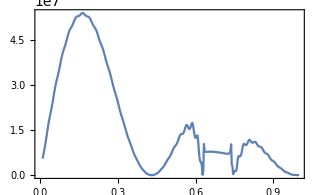
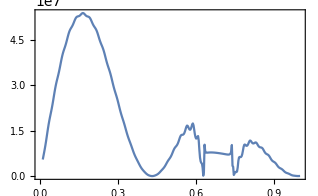

```mathematica
{ListLinePlot[tk0,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[tk0m1,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
tk02=ParallelTable[{x,dProbabPlane[1,x/mee,1/γ,0]},{x,11,18,0.1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained 332.434+464.367 ⅈ and 0.0225361 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.24467×10^7}. NIntegrate obtained -619.429-681.286 ⅈ and 0.0489122 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.48942×10^7}. NIntegrate obtained 1166.92-1085.18 ⅈ and 0.0531897 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.45719×10^7}. NIntegrate obtained -1049.87+942.244 ⅈ and 0.0246899 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.11685×10^7}. NIntegrate obtained 1403.62+442.504 ⅈ and 0.0574778 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.18131×10^7}. NIntegrate obtained -1526.59-450.397 ⅈ and 0.0268764 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.48942×10^7}. NIntegrate obtained 1065.22+1179.94 ⅈ and 0.100125 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained -1599.05-1893.63 ⅈ and 0.194516 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.31925×10^7}. NIntegrate obtained -1491.3+1330.95 ⅈ and 0.107954 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained 1990.87-1471.91 ⅈ and 0.207805 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.28702×10^7}. NIntegrate obtained -1175.98-619.844 ⅈ and 0.115856 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.24956×10^6}. NIntegrate obtained 626.425+1054.45 ⅈ and 0.221913 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.8721×10^7}. NIntegrate obtained 1982.27+2680.07 ⅈ and 0.3599 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.24467×10^7}. NIntegrate obtained -2612.04+1173.71 ⅈ and 0.380563 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained -1832.02-3256.02 ⅈ and 0.645988 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained 486.128-1763.34 ⅈ and 0.407687 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained 3217.53-123.066 ⅈ and 0.684446 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained -2250.62+2568.21 ⅈ and 0.718666 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.65958×10^7}. NIntegrate obtained 881.154+3162.89 ⅈ and 1.09986 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained 485.005-1726.07 ⅈ and 1.82392 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.8721×10^7}. NIntegrate obtained -3491.98-1628.25 ⅈ and 1.16148 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.28702×10^7}. NIntegrate obtained 2866.23+3254.44 ⅈ and 1.92718 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained 4385.48-2971.69 ⅈ and 1.23135 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained -6145.54+2217.64 ⅈ and 2.03664 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

(11. | 304719.
11.1 | 279461.
11.2 | 1.31877×10^6
11.3 | 512705.
11.4 | 125542.
11.5 | 1.01398×10^6
11.6 | 416903.
11.7 | 173895.
11.8 | 936334.
11.9 | 281377.
12. | 264000.
12.1 | 1.20874×10^6
12.2 | 428952.
12.3 | 153690.
12.4 | 998279.
12.5 | 366183.
12.6 | 177109.
12.7 | 838245.
12.8 | 195352.
12.9 | 324498.
13. | 1.08877×10^6
13.1 | 259790.
13.2 | 268007.
13.3 | 1.01484×10^6
13.4 | 257273.
13.5 | 231225.
13.6 | 759894.
13.7 | 106837.
13.8 | 419600.
13.9 | 896155.
14. | 81479.1
14.1 | 473734.
14.2 | 965980.
14.3 | 106007.
14.4 | 373409.
14.5 | 703267.
14.6 | 47134.5
14.7 | 501737.
14.8 | 627169.
14.9 | 2871.81
15. | 697104.
15.1 | 745254.
15.2 | 2059.48
15.3 | 621357.
15.4 | 606349.
15.5 | 18001.3
15.6 | 571041.
15.7 | 376450.
15.8 | 70299.5
15.9 | 774838.
16. | 372218.
16.1 | 92284.6
16.2 | 847623.
16.3 | 370166.
16.4 | 87105.5
16.5 | 674905.
16.6 | 203127.
16.7 | 197535.
16.8 | 649360.
16.9 | 80018.6
17. | 359298.
17.1 | 784258.
17.2 | 72759.6
17.3 | 372615.
17.4 | 709122.
17.5 | 48947.9
17.6 | 362860.
17.7 | 486773.
17.8 | 16706.1
17.9 | 531841.
18. | 426198.)

```mathematica
tk02m=ParallelTable[{x,dProbabPlane[-1,x/mee,1/γ,0]},{x,11,18,0.1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained -2793.18-2204.31 ⅈ and 0.026092 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.564×10^7}. NIntegrate obtained 3256.52+2176.42 ⅈ and 0.0561108 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.45719×10^7}. NIntegrate obtained 1670.05-390.341 ⅈ and 0.0285185 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.48942×10^7}. NIntegrate obtained -2077.26+685.351 ⅈ and 0.0608922 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.18131×10^7}. NIntegrate obtained -819.237+326.726 ⅈ and 0.0310953 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained 815.52-928.859 ⅈ and 0.0659392 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.48942×10^7}. NIntegrate obtained -3756.17-2516.07 ⅈ and 0.113817 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained 4097.79+3301.84 ⅈ and 0.219223 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.45719×10^7}. NIntegrate obtained 2956.87-929.56 ⅈ and 0.122666 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.28702×10^7}. NIntegrate obtained -4342.25+962.25 ⅈ and 0.234918 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.0745×10^7}. NIntegrate obtained 1279.86-3545.97 ⅈ and 0.251625 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.28702×10^7}. NIntegrate obtained -904.662+2029.06 ⅈ and 0.132053 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.8721×10^7}. NIntegrate obtained -3958.68-4523.45 ⅈ and 0.403549 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained 6093.56-511.573 ⅈ and 0.430082 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained 3037.49+5829.4 ⅈ and 0.714869 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained -2269.15+5181.93 ⅈ and 0.459151 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained -7685.83-669.5 ⅈ and 0.759424 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.97892×10^7}. NIntegrate obtained 4180.56-6312.13 ⅈ and 0.805781 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.45719×10^7}. NIntegrate obtained -1371.15-6280. ⅈ and 1.21921 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.8721×10^7}. NIntegrate obtained 8153.14+2501.23 ⅈ and 1.29087 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained -6956.76+6097.76 ⅈ and 1.36669 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained -191.227+4281.74 ⅈ and 2.01614 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.28702×10^7}. NIntegrate obtained -6354.05-4108.33 ⅈ and 2.12821 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.45719×10^7}. NIntegrate obtained 9762.51-3843.13 ⅈ and 2.24587 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

(11. | 387536.
11.1 | 28098.2
11.2 | 319086.
11.3 | 78167.2
11.4 | 194749.
11.5 | 709389.
11.6 | 328555.
11.7 | 254926.
11.8 | 788069.
11.9 | 379902.
12. | 35145.
12.1 | 335693.
12.2 | 84567.3
12.3 | 163096.
12.4 | 598772.
12.5 | 222810.
12.6 | 279197.
12.7 | 796181.
12.8 | 328316.
12.9 | 77245.8
13. | 393225.
13.1 | 86806.4
13.2 | 146631.
13.3 | 456256.
13.4 | 95411.9
13.5 | 349827.
13.6 | 759504.
13.7 | 218387.
13.8 | 191149.
13.9 | 491611.
14. | 79505.9
14.1 | 144551.
14.2 | 320689.
14.3 | 15956.2
14.4 | 413883.
14.5 | 590988.
14.6 | 96989.
14.7 | 396826.
14.8 | 550714.
14.9 | 45319.5
15. | 205958.
15.1 | 255386.
15.2 | 4762.63
15.3 | 396870.
15.4 | 317048.
15.5 | 71538.6
15.6 | 588974.
15.7 | 437414.
15.8 | 43200.1
15.9 | 391899.
16. | 239129.
16.1 | 20303.7
16.2 | 324017.
16.3 | 101075.
16.4 | 152494.
16.5 | 569319.
16.6 | 179973.
16.7 | 193917.
16.8 | 574957.
16.9 | 150235.
17. | 107514.
17.1 | 329608.
17.2 | 24089.
17.3 | 212114.
17.4 | 339062.
17.5 | 22360.5
17.6 | 408569.
17.7 | 482032.
17.8 | 41149.2
17.9 | 361276.
18. | 358150.)

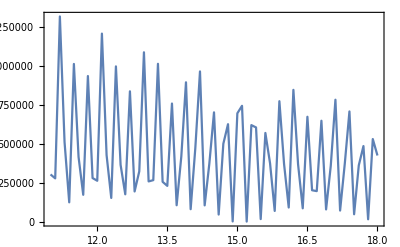
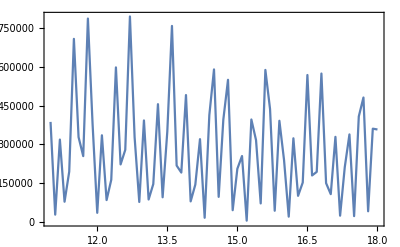

```mathematica
{ListLinePlot[tk02,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[tk02m,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
ParallelTable[dProbabPlane[1,x/mee,1/γ,1/γ],{x,1,2,0.05}]//AbsoluteTiming
```

{16.6569,{6.32595×10^6,8.04833×10^6,7.60734×10^6,5.34935×10^6,2.45492×10^6,385906.,156093.,1.72039×10^6,4.04096×10^6,5.75948×10^6,5.92241×10^6,4.44712×10^6,2.18014×10^6,407201.,79109.,1.29921×10^6,3.31154×10^6,4.9242×10^6,5.19799×10^6,4.00629×10^6,2.06202×10^6}}

```mathematica
(*старое*)
```